```mathematica
(* ::Title::*)(*Direct Odlyzko–te Riele 1985 Benchmark Test*)ClearAll["Global`*"];

SetDirectory["/Users/apple/Documents/Wolfram Mathematica/"];

$MaxExtraPrecision=10000;

workingPrecision=250;
nTerms=2000;

Print["=== DIRECT ODLYZKO–TE RIELE 1985 TEST ==="];

(* ================================================================*)
(*1. Robust high-precision importer*)
(* ================================================================*)

ClearAll[ImportHighPrec];

ImportHighPrec[fileName_String]:=Module[{rawText,tokens},If[!FileExistsQ[fileName],Print["ERROR: File not found: ",FileNameJoin[{$Path,fileName}]];
Abort[];];
rawText=Import[fileName,"String"];
(*Accept spaces,tabs,newlines,and commas as separators.*)tokens=StringSplit[StringTrim[rawText],RegularExpression["[\\s,]+"]];
tokens=Select[tokens,StringLength[#]>0&];
Map[ToExpression[#<>"`"<>ToString[workingPrecision]]&,tokens]];

(* ================================================================*)
(*2. Import synchronized data*)
(* ================================================================*)

Print["Parsing zeros..."];
zerosAll=ImportHighPrec["high_prec_zeros.txt"];

Print["Parsing amplitudes..."];
alphasAll=ImportHighPrec["high_prec_alpha.txt"];

Print["Parsing phases..."];
psiAll=ImportHighPrec["high_prec_arg.txt"];

availableTerms=Min[Length[zerosAll],Length[alphasAll],Length[psiAll]];

If[availableTerms<nTerms,Print["ERROR: At least ",nTerms," synchronized entries are required, but only ",availableTerms," were found."];
Abort[];];

zeros=zerosAll[[1;;nTerms]];
alphas=alphasAll[[1;;nTerms]];
psi=psiAll[[1;;nTerms]];

Print["Loaded ",nTerms," synchronized spectral entries."];

(*Basic data checks.*)

If[!And@@(NumericQ/@zeros)||!And@@(NumericQ/@alphas)||!And@@(NumericQ/@psi),Print["ERROR: One or more imported arrays contain nonnumeric entries."];
Abort[];];

If[!OrderedQ[zeros],Print["WARNING: The zero ordinates are not strictly ordered."];];

Print["First zero ordinate: ",N[First[zeros],20]];
Print["2000th zero ordinate: ",N[Last[zeros],20]];
Print["First amplitude:      ",N[First[alphas],20]];
Print["First phase:          ",N[First[psi],20]];

(* ================================================================*)
(*3. Odlyzko–te Riele kernel*)
(* ================================================================*)

ClearAll[g];

g[t_?NumericQ]:=If[Abs[t]<=1,(1-Abs[t]) Cos[Pi t]+Sin[Pi Abs[t]]/Pi,0];

(*Fixed historical cutoff:height of the 2000th zero.*)

T1985=zeros[[2000]];

kernelWeights=SetPrecision[g/@(zeros/T1985),workingPrecision];

weightedAmplitudes=SetPrecision[kernelWeights*alphas,workingPrecision];

Print["Kernel cutoff T = ",N[T1985,30]];
Print["Nonzero kernel terms: ",Count[kernelWeights,x_/;x!=0]];

(*The 2000th term itself has zero weight because g[1]=0.*)

Print["Final kernel weight g[1] = ",Last[kernelWeights]];

(* ================================================================*)
(*4. Define h_K(y)*)
(* ================================================================*)

ClearAll[h1985];

h1985[y_?NumericQ]:=Module[{yHigh,angles},yHigh=SetPrecision[y,workingPrecision];
angles=zeros*yHigh-psi;
2 Total[weightedAmplitudes*Cos[angles]]];

(*Equivalent dot-product form,retained as an independent coding check of the summation implementation.*)

ClearAll[h1985Dot];

h1985Dot[y_?NumericQ]:=Module[{yHigh},yHigh=SetPrecision[y,workingPrecision];
2 weightedAmplitudes.Cos[zeros*yHigh-psi]];

(* ================================================================*)
(*5. Published Table 3 coordinates*)
(* ================================================================*)

(*Positive-side result:h_K(yPositive) approximately 1.061545.The coordinates are entered as exact rational numbers before conversion to arbitrary precision.This avoids machine-precision contamination.*)

yPositiveExact=-(14045289680592998046790361630399781127400591999789738039965960762*10^6+521505)/10^6;

yPositive=N[yPositiveExact,120];

(*Negative-side result:h_K(yNegative) approximately-1.009749.*)

yNegativeExact=(32097025772922655869740000186211307099797144540349062682805321651*10^6+697419)/10^6;

yNegative=N[yNegativeExact,120];

(* ================================================================*)
(*6. Direct evaluations*)
(* ================================================================*)

Print["\n=== POSITIVE-SIDE BENCHMARK ==="];
Print["Published y = ",ScientificForm[yPositive,30]];

positiveResult=h1985[yPositive];
positiveResultDot=h1985Dot[yPositive];

Print["Direct Total result: ",N[positiveResult,40]];

Print["Dot-product result:  ",N[positiveResultDot,40]];

Print["Implementation difference: ",ScientificForm[N[positiveResult-positiveResultDot,20]]];

Print["Difference from reported 1.061545: ",N[positiveResult-1.061545,30]];

Print["\n=== NEGATIVE-SIDE BENCHMARK ==="];
Print["Published y = ",ScientificForm[yNegative,30]];

negativeResult=h1985[yNegative];
negativeResultDot=h1985Dot[yNegative];

Print["Direct Total result: ",N[negativeResult,40]];

Print["Dot-product result:  ",N[negativeResultDot,40]];

Print["Implementation difference: ",ScientificForm[N[negativeResult-negativeResultDot,20]]];

Print["Difference from reported -1.009749: ",N[negativeResult+1.009749,30]];

(* ================================================================*)
(*7. Automatic interpretation*)
(* ================================================================*)

Print["\n=== AUTOMATIC INTERPRETATION ==="];

Which[Abs[positiveResult-1.061545]<0.001,Print["PASS: The positive-side result reproduces the published ","Odlyzko–te Riele value to within 0.001."],Abs[positiveResult+1.061545]<0.001,Print["SIGN-CONVENTION WARNING: The magnitude is reproduced, but with ","the opposite sign. Check the phase or global sign convention."],Abs[2 positiveResult-1.061545]<0.001,Print["FACTOR WARNING: The calculated value is approximately half ","the published value. Check whether the conjugate-pair factor 2 ","has been applied exactly once."],Abs[positiveResult/2-1.061545]<0.001,Print["FACTOR WARNING: The calculated value is approximately twice ","the published value. Check whether conjugate pairs have been ","counted twice."],True,Print["FAIL: The supplied spectral data do not directly reproduce ","the published positive-side benchmark under this convention."]];

Print["\nTest complete."];
```

=== DIRECT ODLYZKO–TE RIELE 1985 TEST ===

Parsing zeros...

Parsing amplitudes...

Parsing phases...

Loaded 2000 synchronized spectral entries.

First zero ordinate: 14.13472514173469379

2000th zero ordinate: 2515.28648292471288

First amplitude:      0.089141521385034499199

First phase:          1.6933111152043717402

Kernel cutoff T = 2515.28648292471288003818988652

Nonzero kernel terms: 1999

Final kernel weight g[1] = 0

=== POSITIVE-SIDE BENCHMARK ===

Published y = -1.40452896805929980467903616304×10^64

Direct Total result: 1.061545873833283276083994861863251382488

Dot-product result:  1.061545873833283276083994861863251382488

Implementation difference: 0.×10^-182

Difference from reported 1.061545: 8.73833×10^-7

=== NEGATIVE-SIDE BENCHMARK ===

Published y = 3.20970257729226558697400001862×10^64

Direct Total result: -1.009749344320600939595194065833690863998

Dot-product result:  -1.009749344320600939595194065833690863998

Implementation difference: 0.×10^-182

Difference from reported -1.009749: -3.44321×10^-7

=== AUTOMATIC INTERPRETATION ===

PASS: The positive-side result reproduces the published Odlyzko–te Riele value to within 0.001.

Test complete.

```mathematica
(* ::Title::*)(*ANDERSON-STARK MERTENS+/-2 BARRIER RECONNAISSANCE SCANNER*)ClearAll["Global`*"];

SetDirectory["/Users/apple/Documents/Wolfram Mathematica/"];

$MaxExtraPrecision=10000;

workingPrecision=250;
targetBarrier=2;

Print["======================================================"];
Print[" ANDERSON-STARK +/-2 BARRIER RECONNAISSANCE SCANNER"];
Print["======================================================"];

(* ================================================================*)
(*1. Robust arbitrary-precision importer*)
(* ================================================================*)

ClearAll[ImportHighPrec];

ImportHighPrec[fileName_String]:=Module[{rawText,tokens},If[!FileExistsQ[fileName],Print["ERROR: File not found: ",fileName];
Abort[];];
rawText=Import[fileName,"String"];
(*Accept spaces,commas,tabs,and line breaks.*)tokens=StringSplit[StringTrim[rawText],RegularExpression["[\\s,]+"]];
tokens=Select[tokens,StringLength[#]>0&];
Map[ToExpression[#<>"`"<>ToString[workingPrecision]]&,tokens]];

(* ================================================================*)
(*2. Load zeros and amplitudes*)
(* ================================================================*)

Print["\n=== 1. LOADING SPECTRAL DATA ==="];

Print["Parsing zero ordinates..."];
zerosAll=ImportHighPrec["high_prec_zeros.txt"];

Print["Parsing amplitudes..."];
alphasAll=ImportHighPrec["high_prec_alpha.txt"];

availableTerms=Min[Length[zerosAll],Length[alphasAll]];

zeros=zerosAll[[1;;availableTerms]];
alphas=alphasAll[[1;;availableTerms]];

If[availableTerms<2001,Print["ERROR: At least 2001 synchronized zeros and amplitudes ","are required."];
Abort[];];

If[!And@@(NumericQ/@zeros)||!And@@(NumericQ/@alphas),Print["ERROR: A data array contains nonnumeric entries."];
Abort[];];

If[!OrderedQ[zeros],Print["WARNING: Zero ordinates are not sorted increasingly. ","Sorting synchronized zero-amplitude pairs..."];
sortedPairs=SortBy[Transpose[{zeros,alphas}],First];
zeros=sortedPairs[[All,1]];
alphas=sortedPairs[[All,2]];];

Print["Loaded ",availableTerms," synchronized entries."];
Print["First zero: ",N[First[zeros],20]];
Print["Last zero:  ",N[Last[zeros],20]];
Print["First alpha: ",N[First[alphas],20]];

(* ================================================================*)
(*3. Validate amplitude convention*)
(* ================================================================*)

expectedFirstAlpha=0.0891415213850344991987733866481609564463121559756463`60;

alphaConventionError=Abs[First[alphas]-expectedFirstAlpha];

Print["First-amplitude convention error: ",ScientificForm[N[alphaConventionError,10]]];

If[alphaConventionError>10^-20,Print["WARNING: The first amplitude does not match ","1/|rho zeta'(rho)| under the expected convention."];];

(* ================================================================*)
(*4. Permissible kernels*)
(* ================================================================*)

ClearAll[improvedKernel,fejerKernel];

(*Odlyzko-te Riele/Best-Trudgian improved kernel.*)

improvedKernel[t_?NumericQ]:=If[Abs[t]<1,(1-Abs[t]) Cos[Pi t]+Sin[Pi Abs[t]]/Pi,0];

(*Classical Fejer kernel,included for comparison.*)

fejerKernel[t_?NumericQ]:=If[Abs[t]<1,1-Abs[t],0];

kernelFunction=improvedKernel;
kernelName="Improved Odlyzko-te Riele kernel";

Print["Selected kernel: ",kernelName];

(* ================================================================*)
(*5. Anderson-Stark score functions*)
(* ================================================================*)

ClearAll[andersonStarkFactor,boundScore,requiredUniformN];

andersonStarkFactor[N_Integer?Positive]:=2 N/(N+1);

andersonStarkFactor[Infinity]:=2;

boundScore[rawSum_?NumericQ,N_Integer?Positive]:=andersonStarkFactor[N] rawSum;

boundScore[rawSum_?NumericQ,Infinity]:=2 rawSum;

(*For targetBarrier=2,solve (2 N/(N+1)) rawSum>2 for the smallest positive integer N.More generally:N (2 rawSum-targetBarrier)>targetBarrier.*)

requiredUniformN[rawSum_?NumericQ,barrier_?NumericQ]:=Module[{denominator},denominator=2 rawSum-barrier;
If[denominator<=0,Infinity,Floor[barrier/denominator]+1]];

(* ================================================================*)
(*6. Evaluate one cutoff L*)
(* ================================================================*)

ClearAll[scanCutoff];

scanCutoff[L_Integer,maximumSelected_Integer]:=Module[{T,localZeros,localAlphas,kernelWeights,contributions,ranking,sortedContributions,sortedIndices,cumulativeSums,nLimit,records,rawSum,requiredN,attainedBound,theoreticalCeiling},If[L>=availableTerms,Print["Cutoff L = ",L," skipped because the next zero is unavailable."];
Return[{}];];
(*Choose T strictly between gamma_L and gamma_(L+1).Hence Gamma intersection[0,T] consists exactly of the first L positive ordinates.*)T=SetPrecision[(zeros[[L]]+zeros[[L+1]])/2,workingPrecision];
localZeros=zeros[[1;;L]];
localAlphas=alphas[[1;;L]];
kernelWeights=SetPrecision[kernelFunction/@(localZeros/T),workingPrecision];
contributions=SetPrecision[localAlphas*kernelWeights,workingPrecision];
(*Sort from heaviest to lightest contribution.*)ranking=Reverse@Ordering[contributions];
sortedIndices=ranking;
sortedContributions=contributions[[ranking]];
cumulativeSums=Accumulate[sortedContributions];
nLimit=Min[maximumSelected,L];
records=Table[rawSum=cumulativeSums[[n]];
requiredN=requiredUniformN[rawSum,targetBarrier];
attainedBound=If[requiredN===Infinity,2 rawSum,boundScore[rawSum,requiredN]];
theoreticalCeiling=2 rawSum;
<|"CutoffCountL"->L,"CutoffT"->N[T,25],"SelectedCountN"->n,"RawWeightedSum"->N[rawSum,30],"InfiniteIndependenceCeiling"->N[theoreticalCeiling,30],"RequiredUniformIndependenceN"->requiredN,"BoundAtRequiredN"->N[attainedBound,30],"CrossesPlus2Conditionally"->If[requiredN===Infinity,False,attainedBound>targetBarrier]|>,{n,1,nLimit}];
records];

(* ================================================================*)
(*7. Best-Trudgian benchmark*)
(* ================================================================*)

Print["\n=== 2. BEST-TRUDGIAN BENCHMARK ==="];

benchmarkL=2000;
benchmarkSelected=500;
benchmarkIndependenceN=4976;

benchmarkT=(zeros[[benchmarkL]]+zeros[[benchmarkL+1]])/2;

benchmarkWeights=alphas[[1;;benchmarkL]]*(kernelFunction/@(zeros[[1;;benchmarkL]]/benchmarkT));

benchmarkRanking=Reverse@Ordering[benchmarkWeights];

benchmarkRawSum=Total[benchmarkWeights[[benchmarkRanking[[1;;benchmarkSelected]]]]];

benchmarkBound=boundScore[benchmarkRawSum,benchmarkIndependenceN];

benchmarkInfiniteCeiling=2 benchmarkRawSum;

Print["L = ",benchmarkL];
Print["Selected zeros = ",benchmarkSelected];
Print["Uniform N_gamma = ",benchmarkIndependenceN];

Print["Raw weighted sum = ",N[benchmarkRawSum,30]];

Print["Anderson-Stark bound = ",N[benchmarkBound,30]];

Print["Infinite-N ceiling = ",N[benchmarkInfiniteCeiling,30]];

Print["Difference from 1.6383 = ",N[benchmarkBound-1.6383,20]];

If[Abs[benchmarkBound-1.6383]<0.01,Print["BENCHMARK PASS: The implementation is consistent ","with the published Best-Trudgian scale."],Print["BENCHMARK WARNING: The result differs materially ","from 1.6383. Check T, sorting, kernel, and data."]];

(* ================================================================*)
(*8. Configure the 100,000-zero reconnaissance scan*)
(* ================================================================*)

Print["\n=== 3. CONFIGURING BARRIER SCAN ==="];

(*Every cutoff L requires gamma_(L+1),so with exactly 100,000 zeros the largest possible L is 99,999.*)

suggestedCutoffs={2000,5000,9000,10000,15000,20000,30000,40000,50000,60000,75000,90000,99999};

cutoffCounts=Select[suggestedCutoffs,1<=#<availableTerms&];

(*Increase this later if desired.The first scan through 5000 selected zeros is fast because it requires no lattice reduction.*)

maximumSelectedZeros=Min[5000,availableTerms-1];

Print["Cutoffs to scan: ",cutoffCounts];
Print["Maximum selected zeros per cutoff: ",maximumSelectedZeros];

(* ================================================================*)
(*9. Execute reconnaissance*)
(* ================================================================*)

Print["\n=== 4. EXECUTING ANDERSON-STARK SCORE SCAN ==="];

allReconnaissanceRecords=Flatten[Table[Print["Scanning L = ",L," with T between gamma_",L," and gamma_",L+1,"..."];
scanCutoff[L,maximumSelectedZeros],{L,cutoffCounts}],1];

Print["Generated ",Length[allReconnaissanceRecords]," candidate records."];

(* ================================================================*)
(*10. Isolate configurations theoretically capable of crossing 2*)
(* ================================================================*)

barrierCandidates=Select[allReconnaissanceRecords,TrueQ[#["CrossesPlus2Conditionally"]]&];

Print["\nNumber of conditional barrier-crossing configurations: ",Length[barrierCandidates]];

(*Rank primarily by smallest required independence coefficient,then by smallest selected set,and finally by larger raw sum.*)

rankedBarrierCandidates=SortBy[barrierCandidates,{#["RequiredUniformIndependenceN"]&,#["SelectedCountN"]&,-#["RawWeightedSum"]&}];

topCandidateCount=Min[25,Length[rankedBarrierCandidates]];

topCandidates=If[topCandidateCount>0,Take[rankedBarrierCandidates,topCandidateCount],{}];

(* ================================================================*)
(*11. Display top candidates*)
(* ================================================================*)

Print["\n=== 5. TOP CONDITIONAL +/-2 BARRIER CANDIDATES ==="];

If[Length[topCandidates]==0,Print["No configuration within the present scan can cross 2, ","even under its computed required uniform N."],Print[Grid[Prepend[Table[{candidate["CutoffCountL"],candidate["SelectedCountN"],NumberForm[candidate["RawWeightedSum"],{12,9}],NumberForm[candidate["InfiniteIndependenceCeiling"],{12,9}],candidate["RequiredUniformIndependenceN"],NumberForm[candidate["BoundAtRequiredN"],{12,9}]},{candidate,topCandidates}],{"L","Selected n","Raw Sum S","2 S Ceiling","Required N_gamma","Bound at Required N"}],Frame->All,Background->{None,{LightGray,None}},Alignment->Left]]];
(* ================================================================*)(*12. Extract complete data for the best candidate*)(* ================================================================*)If[Length[rankedBarrierCandidates]>0,bestCandidate=First[rankedBarrierCandidates];
bestL=bestCandidate["CutoffCountL"];
bestNSelected=bestCandidate["SelectedCountN"];
bestRequiredIndependence=bestCandidate["RequiredUniformIndependenceN"];
bestT=SetPrecision[(zeros[[bestL]]+zeros[[bestL+1]])/2,workingPrecision];
bestKernelWeights=kernelFunction/@(zeros[[1;;bestL]]/bestT);
bestContributions=alphas[[1;;bestL]]*bestKernelWeights;
bestRanking=Reverse@Ordering[bestContributions];
bestSelectedIndices=bestRanking[[1;;bestNSelected]];
bestSelectedZeros=zeros[[bestSelectedIndices]];
bestSelectedAlphas=alphas[[bestSelectedIndices]];
bestSelectedContributions=bestContributions[[bestSelectedIndices]];
Print["\n=== 6. BEST CANDIDATE DETAILS ==="];
Print["Ambient zero count L: ",bestL];
Print["Selected zero count n: ",bestNSelected];
Print["Cutoff T: ",N[bestT,30]];
Print["Required uniform N_gamma: ",bestRequiredIndependence];
Print["Raw weighted sum S: ",bestCandidate["RawWeightedSum"]];
Print["Infinite-N ceiling 2 S: ",bestCandidate["InfiniteIndependenceCeiling"]];
Print["Conditional Anderson-Stark bound: ",bestCandidate["BoundAtRequiredN"]];
Print["If the required independence is certified, then:"];
Print["limsup M(x)/Sqrt[x] >= ",bestCandidate["BoundAtRequiredN"]];
Print["liminf M(x)/Sqrt[x] <= -",bestCandidate["BoundAtRequiredN"]];
bestCandidateDataset=Table[<|"Rank"->rank,"OriginalZeroIndex"->bestSelectedIndices[[rank]],"Gamma"->N[bestSelectedZeros[[rank]],50],"Alpha"->N[bestSelectedAlphas[[rank]],50],"KernelWeight"->N[bestKernelWeights[[bestSelectedIndices[[rank]]]],50],"WeightedContribution"->N[bestSelectedContributions[[rank]],50]|>,{rank,1,bestNSelected}];
Export["Anderson_Stark_Best_Candidate_Selected_Zeros.csv",Prepend[Values/@bestCandidateDataset,Keys[First[bestCandidateDataset]]],"CSV"];
Export["Anderson_Stark_Best_Candidate.mx",<|"CandidateSummary"->bestCandidate,"CutoffT"->bestT,"SelectedIndices"->bestSelectedIndices,"SelectedZeros"->bestSelectedZeros,"SelectedAlphas"->bestSelectedAlphas,"SelectedContributions"->bestSelectedContributions|>];];
(* ================================================================*)(*13. Export all reconnaissance results*)(* ================================================================*)If[Length[allReconnaissanceRecords]>0,Export["Anderson_Stark_All_Reconnaissance_Results.csv",Prepend[Values/@allReconnaissanceRecords,Keys[First[allReconnaissanceRecords]]],"CSV"];];
If[Length[rankedBarrierCandidates]>0,Export["Anderson_Stark_Ranked_Barrier_Candidates.csv",Prepend[Values/@rankedBarrierCandidates,Keys[First[rankedBarrierCandidates]]],"CSV"];];
Print["\n======================================================"];
Print[" RECONNAISSANCE COMPLETE"];
Print["======================================================"];
Print["Saved: Anderson_Stark_All_Reconnaissance_Results.csv"];
If[Length[rankedBarrierCandidates]>0,Print["Saved: Anderson_Stark_Ranked_Barrier_Candidates.csv"];
Print["Saved: Anderson_Stark_Best_Candidate_Selected_Zeros.csv"];
Print["Saved: Anderson_Stark_Best_Candidate.mx"];];
Print["\nIMPORTANT STATUS:"];
Print["A score above 2 is presently CONDITIONAL, not certified."];
Print["The next stage must certify the required {N_gamma}-independence ","of the selected ordinates relative to every zero below T."];
```

======================================================

ANDERSON-STARK +/-2 BARRIER RECONNAISSANCE SCANNER

======================================================

=== 1. LOADING SPECTRAL DATA ===

Parsing zero ordinates...

Parsing amplitudes...

Loaded 100000 synchronized entries.

First zero: 14.13472514173469379

Last zero:  74920.827498994186794

First alpha: 0.089141521385034499199

First-amplitude convention error: 3.2868810×10^-54

Selected kernel: Improved Odlyzko-te Riele kernel

=== 2. BEST-TRUDGIAN BENCHMARK ===

L = 2000

Selected zeros = 500

Uniform N_gamma = 4976

Raw weighted sum = 0.819290930628169035768480444112

Anderson-Stark bound = 1.63825263042224999878800831421

Infinite-N ceiling = 1.63858186125633807153696088822

Difference from 1.6383 = -0.0000473696

BENCHMARK PASS: The implementation is consistent with the published Best-Trudgian scale.

=== 3. CONFIGURING BARRIER SCAN ===

Cutoffs to scan: {2000,5000,9000,10000,15000,20000,30000,40000,50000,60000,75000,90000,99999}

Maximum selected zeros per cutoff: 5000

=== 4. EXECUTING ANDERSON-STARK SCORE SCAN ===

Scanning L = 2000 with T between gamma_2000 and gamma_2001...

Scanning L = 5000 with T between gamma_5000 and gamma_5001...

Scanning L = 9000 with T between gamma_9000 and gamma_9001...

Scanning L = 10000 with T between gamma_10000 and gamma_10001...

Scanning L = 15000 with T between gamma_15000 and gamma_15001...

Scanning L = 20000 with T between gamma_20000 and gamma_20001...

Scanning L = 30000 with T between gamma_30000 and gamma_30001...

Scanning L = 40000 with T between gamma_40000 and gamma_40001...

Scanning L = 50000 with T between gamma_50000 and gamma_50001...

Scanning L = 60000 with T between gamma_60000 and gamma_60001...

Scanning L = 75000 with T between gamma_75000 and gamma_75001...

Scanning L = 90000 with T between gamma_90000 and gamma_90001...

Scanning L = 99999 with T between gamma_99999 and gamma_100000...

Generated 62000 candidate records.

Number of conditional barrier-crossing configurations: 48659

=== 5. TOP CONDITIONAL +/-2 BARRIER CANDIDATES ===

L | Selected n | Raw Sum S | 2 S Ceiling | Required N_gamma | Bound at Required N
99999 | 4331 | 1.333372187 | 2.666744374 | 3 | 2.000058280
99999 | 4332 | 1.333421381 | 2.666842762 | 3 | 2.000132072
99999 | 4333 | 1.333470563 | 2.666941126 | 3 | 2.000205845
99999 | 4334 | 1.333519730 | 2.667039459 | 3 | 2.000279594
99999 | 4335 | 1.333568892 | 2.667137785 | 3 | 2.000353338
99999 | 4336 | 1.333618046 | 2.667236093 | 3 | 2.000427070
99999 | 4337 | 1.333667192 | 2.667334384 | 3 | 2.000500788
99999 | 4338 | 1.333716335 | 2.667432670 | 3 | 2.000574502
99999 | 4339 | 1.333765473 | 2.667530946 | 3 | 2.000648209
99999 | 4340 | 1.333814603 | 2.667629206 | 3 | 2.000721905
99999 | 4341 | 1.333863733 | 2.667727466 | 3 | 2.000795599
99999 | 4342 | 1.333912860 | 2.667825720 | 3 | 2.000869290
99999 | 4343 | 1.333961965 | 2.667923931 | 3 | 2.000942948
99999 | 4344 | 1.334011069 | 2.668022139 | 3 | 2.001016604
99999 | 4345 | 1.334060156 | 2.668120313 | 3 | 2.001090234
99999 | 4346 | 1.334109237 | 2.668218473 | 3 | 2.001163855
99999 | 4347 | 1.334158314 | 2.668316629 | 3 | 2.001237472
99999 | 4348 | 1.334207377 | 2.668414754 | 3 | 2.001311065
99999 | 4349 | 1.334256435 | 2.668512871 | 3 | 2.001384653
99999 | 4350 | 1.334305487 | 2.668610973 | 3 | 2.001458230
99999 | 4351 | 1.334354528 | 2.668709057 | 3 | 2.001531793
99999 | 4352 | 1.334403565 | 2.668807129 | 3 | 2.001605347
99999 | 4353 | 1.334452600 | 2.668905201 | 3 | 2.001678900
99999 | 4354 | 1.334501596 | 2.669003192 | 3 | 2.001752394
99999 | 4355 | 1.334550564 | 2.669101128 | 3 | 2.001825846

=== 6. BEST CANDIDATE DETAILS ===

Ambient zero count L: 99999

Selected zero count n: 4331

Cutoff T: 74920.5436461265391151995249022

Required uniform N_gamma: 3

Raw weighted sum S: 1.33337218677142668904383519064

Infinite-N ceiling 2 S: 2.66674437354285337808767038129

Conditional Anderson-Stark bound: 2.00005828015714003356575278597

If the required independence is certified, then:

limsup M(x)/Sqrt[x] >= 2.00005828015714003356575278597

liminf M(x)/Sqrt[x] <= -2.00005828015714003356575278597

======================================================

RECONNAISSANCE COMPLETE

======================================================

Saved: Anderson_Stark_All_Reconnaissance_Results.csv

Saved: Anderson_Stark_Ranked_Barrier_Candidates.csv

Saved: Anderson_Stark_Best_Candidate_Selected_Zeros.csv

Saved: Anderson_Stark_Best_Candidate.mx

IMPORTANT STATUS:

A score above 2 is presently CONDITIONAL, not certified.

The next stage must certify the required {N_gamma}-independence of the selected ordinates relative to every zero below T.

```mathematica
(* ::Title::*)(*ANDERSON-STARK+/-2 PROOF-ORIENTED CERTIFICATION STAGE*)(*Run this block AFTER the reconnaissance scanner.*)Print[""];
Print["=============================================================="];
Print[" ANDERSON-STARK PROOF-ORIENTED CERTIFICATION STAGE"];
Print["=============================================================="];

(* ================================================================*)
(*0. User configuration*)
(* ================================================================*)

targetBarrier=2;

(*Prefer a visible margin,not merely 2.000000...*)
desiredSafetyMargin=10^-3;

(*Maximum acceptable uniform independence requirement when searching for a practical candidate.*)
maximumPreferredNgamma=10^6;

(*Decimal scaling exponent K=10^k used in the relation lattice.With approximately 250-digit input data,do not use k near 250. Retain a substantial accuracy guard.*)
requestedKDigits=180;
accuracyGuardDigits=30;

(*Certification modes:"Pilot":High-precision numerical Gram-Schmidt.Useful for screening,but not a rigorous proof."Exact":Exact rational Gram-Schmidt on the integer LLL output.Potentially extremely expensive in high dimension.*)
certificationMode="Pilot";

(*Set True only after a candidate passes the base condition.Full certification requires one augmented LLL reduction for every unselected ambient zero below T.*)
runFullAmbientCertification=False;

(*If True,resume from the saved checkpoint.*)
resumeFromCheckpoint=True;

(*Save after this many ambient tests.*)
checkpointInterval=25;

checkpointFile="Anderson_Stark_Certification_Checkpoint.mx";

certificateFile="Anderson_Stark_Final_Certificate.mx";

summaryCSV="Anderson_Stark_Proof_Candidates.csv";

(*Prevent accidental attempts at huge exact Gram-Schmidt jobs.*)
exactDimensionWarning=350;

(*Display this many candidate rows.*)
numberCandidatesToDisplay=30;

(* ================================================================*)
(*1. Verify that reconnaissance variables exist*)
(* ================================================================*)

requiredSymbols={barrierCandidates,zeros,alphas,kernelFunction,availableTerms};

If[!And@@(ValueQ/@requiredSymbols),Print["ERROR: Required reconnaissance variables are unavailable."];
Print["Run the Anderson-Stark reconnaissance scanner first."];
Abort[];];

If[Length[barrierCandidates]==0,Print["No conditional barrier-crossing candidates exist."];
Abort[];];

Print["Available conditional candidates: ",Length[barrierCandidates]];

(* ================================================================*)
(*2. Add margin and cost-related fields*)
(* ================================================================*)

ClearAll[augmentCandidate];

augmentCandidate[c_Association]:=Module[{margin,nSelected,ambientL,requiredN,roughCostLog},margin=c["BoundAtRequiredN"]-targetBarrier;
nSelected=c["SelectedCountN"];
ambientL=c["CutoffCountL"];
requiredN=c["RequiredUniformIndependenceN"];
(*This is only a ranking heuristic,not a runtime theorem.Dimension receives the strongest penalty because lattice reduction becomes extremely expensive as n grows.*)roughCostLog=6 Log[10,Max[nSelected,2]]+3 Log[10,Max[If[requiredN===Infinity,10^20,requiredN],2]]+Log[10,Max[ambientL-nSelected,1]];
Join[c,<|"BarrierMargin"->N[margin,30],"RoughCostLog10"->N[roughCostLog,20]|>]];

augmentedCandidates=augmentCandidate/@barrierCandidates;

(* ================================================================*)
(*3. Construct several useful rankings*)
(* ================================================================*)

(*A.Lowest-dimensional crossing,regardless of margin.*)

rankedByDimension=SortBy[augmentedCandidates,{#["SelectedCountN"]&,#["RequiredUniformIndependenceN"]&,#["CutoffCountL"]&,-#["BarrierMargin"]&}];

(*B.Largest numerical margin.*)

rankedByMargin=SortBy[augmentedCandidates,{-#["BarrierMargin"]&,#["SelectedCountN"]&,#["RequiredUniformIndependenceN"]&}];

(*C.Crude practical-cost ranking.*)

rankedByEstimatedCost=SortBy[augmentedCandidates,{#["RoughCostLog10"]&,-#["BarrierMargin"]&}];

(*D.Candidates satisfying preferred margin and N_gamma limits.*)

preferredCandidates=Select[augmentedCandidates,#["BarrierMargin"]>=desiredSafetyMargin&&#["RequiredUniformIndependenceN"]=!=Infinity&&#["RequiredUniformIndependenceN"]<=maximumPreferredNgamma&];

rankedPreferred=SortBy[preferredCandidates,{#["SelectedCountN"]&,#["RoughCostLog10"]&,-#["BarrierMargin"]&}];

(*Choose the candidate for certification.*)

candidateForCertification=Which[Length[rankedPreferred]>0,First[rankedPreferred],Length[rankedByDimension]>0,First[rankedByDimension],True,Print["ERROR: Candidate selection failed."];
Abort[]];

(* ================================================================*)
(*4. Candidate display function*)
(* ================================================================*)

ClearAll[candidateTable];

candidateTable[list_List,count_Integer]:=Module[{takeCount},takeCount=Min[count,Length[list]];
If[takeCount==0,Return[Grid[{{"No candidates"}},Frame->All]]];
Grid[Prepend[Table[{c["CutoffCountL"],c["SelectedCountN"],NumberForm[c["RawWeightedSum"],{14,10}],c["RequiredUniformIndependenceN"],NumberForm[c["BoundAtRequiredN"],{14,10}],ScientificForm[c["BarrierMargin"],5],NumberForm[c["RoughCostLog10"],{10,3}]},{c,Take[list,takeCount]}],{"Ambient L","Selected n","Raw S","Required Nγ","Bound","Margin","Cost Proxy"}],Frame->All,Background->{None,{LightGray,None}},Alignment->Left]];

Print["\n=== LOWEST-DIMENSION CONDITIONAL CROSSINGS ==="];

Print[candidateTable[rankedByDimension,numberCandidatesToDisplay]];

Print["\n=== LARGEST-MARGIN CONDITIONAL CROSSINGS ==="];

Print[candidateTable[rankedByMargin,Min[15,numberCandidatesToDisplay]]];

Print["\n=== PREFERRED PROOF CANDIDATES ==="];

Print[candidateTable[rankedPreferred,numberCandidatesToDisplay]];

(*Export candidate table.*)

If[Length[augmentedCandidates]>0,Export[summaryCSV,Prepend[Values/@rankedByDimension,Keys[First[rankedByDimension]]],"CSV"];];

(* ================================================================*)
(*5. Reconstruct selected set*)
(* ================================================================*)

candidateL=candidateForCertification["CutoffCountL"];

candidateSelectedCount=candidateForCertification["SelectedCountN"];

candidateNgamma=candidateForCertification["RequiredUniformIndependenceN"];

candidateMargin=candidateForCertification["BarrierMargin"];

candidateBound=candidateForCertification["BoundAtRequiredN"];

candidateRawSum=candidateForCertification["RawWeightedSum"];

candidateT=SetPrecision[(zeros[[candidateL]]+zeros[[candidateL+1]])/2,workingPrecision];

candidateKernelWeights=kernelFunction/@(zeros[[1;;candidateL]]/candidateT);

candidateContributions=alphas[[1;;candidateL]]*candidateKernelWeights;

candidateRanking=Reverse@Ordering[candidateContributions];

candidateSelectedIndices=candidateRanking[[1;;candidateSelectedCount]];

candidateSelectedZeros=zeros[[candidateSelectedIndices]];

candidateSelectedAlphas=alphas[[candidateSelectedIndices]];

candidateSelectedContributions=candidateContributions[[candidateSelectedIndices]];

candidateAmbientIndices=Complement[Range[candidateL],candidateSelectedIndices];

Print[""];
Print["=============================================================="];
Print[" SELECTED CERTIFICATION CANDIDATE"];
Print["=============================================================="];

Print["Ambient cutoff count L: ",candidateL];
Print["Selected dimension n:   ",candidateSelectedCount];
Print["Cutoff T:               ",N[candidateT,30]];
Print["Required uniform Nγ:    ",candidateNgamma];
Print["Raw weighted sum S:      ",candidateRawSum];
Print["Conditional bound:       ",candidateBound];
Print["Barrier margin:          ",candidateMargin];

Print["Number of augmented ambient tests required: ",Length[candidateAmbientIndices]];

(* ================================================================*)
(*6. Verify the numerical Anderson-Stark score*)
(* ================================================================*)

recomputedRawSum=Total[candidateSelectedContributions];

recomputedBound=(2 candidateNgamma/(candidateNgamma+1))*recomputedRawSum;

Print["\n=== SCORE RECOMPUTATION ==="];

Print["Stored raw sum:     ",N[candidateRawSum,40]];

Print["Recomputed raw sum: ",N[recomputedRawSum,40]];

Print["Stored bound:       ",N[candidateBound,40]];

Print["Recomputed bound:   ",N[recomputedBound,40]];

Print["Score discrepancy:  ",ScientificForm[N[recomputedBound-candidateBound,20]]];

If[recomputedBound<=targetBarrier,Print["ERROR: Recomputed score does not exceed 2."];
Abort[];];

(* ================================================================*)
(*7. Determine a safe decimal lattice scale*)
(* ================================================================*)

minimumSelectedAccuracy=Min[Accuracy/@candidateSelectedZeros];

maximumSafeKDigits=Floor[minimumSelectedAccuracy-accuracyGuardDigits];

kDigits=Min[requestedKDigits,maximumSafeKDigits];

If[kDigits<=0,Print["ERROR: Insufficient input accuracy for lattice construction."];
Abort[];];

Kscale=10^kDigits;

Print["\n=== PRECISION AUDIT ==="];

Print["Minimum reported accuracy among selected ordinates: ",N[minimumSelectedAccuracy,10]," decimal digits"];

Print["Requested k: ",requestedKDigits];
Print["Maximum guarded k: ",maximumSafeKDigits];
Print["Using K = 10^",kDigits];

If[kDigits<requestedKDigits,Print["WARNING: k was reduced to preserve an accuracy guard."];];

(* ================================================================*)
(*8. Check stability of Floor[K gamma]*)
(* ================================================================*)

ClearAll[scalingAudit];

scalingAudit[values_List,K_Integer]:=Module[{scaled,fractionalDistances,minimumDistance,scaledAccuracies,minimumScaledAccuracy,estimatedUncertainty,stable},scaled=N[K values,workingPrecision];
fractionalDistances=Map[Function[z,Min[FractionalPart[z],1-FractionalPart[z]]],scaled];
minimumDistance=Min[fractionalDistances];
scaledAccuracies=Accuracy/@scaled;
minimumScaledAccuracy=Min[scaledAccuracies];
estimatedUncertainty=10^(-minimumScaledAccuracy);
stable=minimumDistance>100 estimatedUncertainty;
<|"MinimumDistanceToInteger"->minimumDistance,"MinimumScaledAccuracy"->minimumScaledAccuracy,"EstimatedUncertainty"->estimatedUncertainty,"FloorStableHeuristically"->stable|>];

selectedScalingAudit=scalingAudit[candidateSelectedZeros,Kscale];

Print["Minimum distance of K gamma to an integer: ",ScientificForm[N[selectedScalingAudit["MinimumDistanceToInteger"],15]]];

Print["Estimated scaled uncertainty: ",ScientificForm[N[selectedScalingAudit["EstimatedUncertainty"],15]]];

Print["Floor stability test: ",selectedScalingAudit["FloorStableHeuristically"]];

If[!TrueQ[selectedScalingAudit["FloorStableHeuristically"]],Print["ERROR: One or more Floor[K gamma] values may be unstable."];
Print["Reduce kDigits or recompute the zero ordinates at higher accuracy."];
Abort[];];

(* ================================================================*)
(*9. Construct Best-Trudgian relation lattice*)
(* ================================================================*)

ClearAll[relationLatticeBasis];

relationLatticeBasis[ordinates_List,K_Integer]:=Module[{count,scaledOrdinates,identity},count=Length[ordinates];
scaledOrdinates=Floor[K ordinates];
identity=IdentityMatrix[count];
MapThread[Append,{identity,scaledOrdinates}]];

(*A row combination with coefficients a_i has the form {a_1,...,a_n,Sum[a_i Floor[K gamma_i]]}.This is the lattice L(K;S) used to detect short integer relations among the ordinates.*)

(* ================================================================*)
(*10. Gram-Schmidt lower-bound functions*)
(* ================================================================*)

ClearAll[gramSchmidtMinSquaredNumeric,gramSchmidtMinSquaredExact];

gramSchmidtMinSquaredNumeric[basis_List,precision_Integer:150]:=Module[{b,orthogonal,squaredNorms,v,projection,i,j},b=N[basis,precision];
orthogonal={};
squaredNorms={};
For[i=1,i<=Length[b],i++,v=b[[i]];
For[j=1,j<=Length[orthogonal],j++,projection=(v.orthogonal[[j]])/squaredNorms[[j]];
v=v-projection orthogonal[[j]];];
AppendTo[orthogonal,v];
AppendTo[squaredNorms,v.v];];
Min[squaredNorms]];

gramSchmidtMinSquaredExact[basis_List]:=Module[{orthogonal,squaredNorms,v,projection,i,j},orthogonal={};
squaredNorms={};
For[i=1,i<=Length[basis],i++,v=basis[[i]];
For[j=1,j<=Length[orthogonal],j++,projection=Cancel[(v.orthogonal[[j]])/squaredNorms[[j]]];
v=Together[v-projection orthogonal[[j]]];];
AppendTo[orthogonal,v];
AppendTo[squaredNorms,Together[v.v]];];
Min[squaredNorms]];

ClearAll[computeGSMinimum];

computeGSMinimum[reducedBasis_List]:=Switch[certificationMode,"Pilot",gramSchmidtMinSquaredNumeric[reducedBasis,150],"Exact",gramSchmidtMinSquaredExact[reducedBasis],_,Print["ERROR: certificationMode must be \"Pilot\" or \"Exact\"."];
Abort[]];

(* ================================================================*)
(*11. Best-Trudgian thresholds*)
(* ================================================================*)

ClearAll[baseThreshold,augmentedThreshold];

(*Contrapositive of the weak-dependence bound.*)

baseThreshold[n_Integer,Nbound_Integer]:=(n^2+n) Nbound^2+(2 n+2) Nbound+2;

(*Bound for a selected set augmented by one unselected zero.*)

augmentedThreshold[n_Integer,Nbound_Integer]:=(n^2+n) Nbound^2+2 n Nbound+2;

requiredBaseThreshold=baseThreshold[candidateSelectedCount,candidateNgamma];

requiredAugmentedThreshold=augmentedThreshold[candidateSelectedCount,candidateNgamma];

Print["\n=== CERTIFICATION THRESHOLDS ==="];

Print["Base squared-norm threshold:      ",requiredBaseThreshold];

Print["Augmented squared-norm threshold: ",requiredAugmentedThreshold];

Print["Base norm threshold:              ",N[Sqrt[requiredBaseThreshold],20]];

Print["Augmented norm threshold:         ",N[Sqrt[requiredAugmentedThreshold],20]];

(* ================================================================*)
(*12. Dimension warning*)
(* ================================================================*)

If[certificationMode=="Exact"&&candidateSelectedCount>exactDimensionWarning,Print[""];
Print["WARNING: Exact rational Gram-Schmidt in dimension ",candidateSelectedCount," may require extreme time and memory."];
Print["Consider first running certificationMode = \"Pilot\"."];];

(* ================================================================*)
(*13. Base lattice test*)
(* ================================================================*)

Print[""];
Print["=============================================================="];
Print[" BASE INDEPENDENCE TEST"];
Print["=============================================================="];

baseBasis=relationLatticeBasis[candidateSelectedZeros,Kscale];

Print["Base lattice dimensions: ",Dimensions[baseBasis]];

Print["Running LatticeReduce on base lattice..."];

baseTiming=AbsoluteTiming[reducedBaseBasis=LatticeReduce[baseBasis];];

Print["Base LatticeReduce time: ",baseTiming[[1]]," seconds"];

Print["Computing Gram-Schmidt lower bound..."];

baseGSTiming=AbsoluteTiming[baseGSMinimum=computeGSMinimum[reducedBaseBasis];];

Print["Gram-Schmidt time: ",baseGSTiming[[1]]," seconds"];

baseConditionPassed=baseGSMinimum>=requiredBaseThreshold;

Print["Minimum Gram-Schmidt squared norm: ",N[baseGSMinimum,30]];

Print["Required squared threshold:         ",requiredBaseThreshold];

Print["Base independence condition passed: ",baseConditionPassed];

If[!baseConditionPassed,Print[""];
Print["=============================================================="];
Print[" FINAL STATUS: CONDITIONAL ONLY"];
Print["=============================================================="];
Print["The amplitude score exceeds 2, but the chosen lattice ","has not certified the required base N_gamma-independence."];
Export[certificateFile,<|"Status"->"ConditionalOnly-BaseFailed","Candidate"->candidateForCertification,"SelectedIndices"->candidateSelectedIndices,"KDigits"->kDigits,"BaseGSMinimum"->baseGSMinimum,"BaseThreshold"->requiredBaseThreshold,"CertificationMode"->certificationMode|>];
Abort[];];

Print[""];
Print["BASE CONDITION PASSED."];

If[certificationMode=="Pilot",Print["This remains a numerical pilot result because the ","Gram-Schmidt calculation was not exact."];];

(* ================================================================*)
(*14. Optional full ambient certification*)
(* ================================================================*)

If[!runFullAmbientCertification,Print[""];
Print["=============================================================="];
Print[" FINAL STATUS: BASE CONDITION ONLY"];
Print["=============================================================="];
Print["The base relation test passed, but ",Length[candidateAmbientIndices]," augmented ambient-zero tests remain."];
Print["Set runFullAmbientCertification = True to continue."];
Export[certificateFile,<|"Status"->"BaseConditionPassed-AmbientNotRun","Candidate"->candidateForCertification,"SelectedIndices"->candidateSelectedIndices,"SelectedZeros"->candidateSelectedZeros,"KDigits"->kDigits,"BaseGSMinimum"->baseGSMinimum,"BaseThreshold"->requiredBaseThreshold,"CertificationMode"->certificationMode|>];
Abort[];];

(* ================================================================*)
(*15. Initialize or resume ambient tests*)
(* ================================================================*)

Print[""];
Print["=============================================================="];
Print[" FULL AUGMENTED AMBIENT-ZERO CERTIFICATION"];
Print["=============================================================="];

If[resumeFromCheckpoint&&FileExistsQ[checkpointFile],checkpointData=Import[checkpointFile];
ambientStartPosition=checkpointData["NextPosition"];
ambientResults=checkpointData["AmbientResults"];
allAmbientPassed=checkpointData["AllAmbientPassed"];
Print["Resuming from ambient position ",ambientStartPosition];,ambientStartPosition=1;
ambientResults={};
allAmbientPassed=True;];

(* ================================================================*)
(*16. Test every unselected ambient zero*)
(* ================================================================*)

For[ambientPosition=ambientStartPosition,ambientPosition<=Length[candidateAmbientIndices],ambientPosition++,ambientOriginalIndex=candidateAmbientIndices[[ambientPosition]];
ambientGamma=zeros[[ambientOriginalIndex]];
Print["\nAmbient test ",ambientPosition," / ",Length[candidateAmbientIndices]," | zero index ",ambientOriginalIndex];
augmentedOrdinates=Append[candidateSelectedZeros,ambientGamma];
augmentedAudit=scalingAudit[augmentedOrdinates,Kscale];
If[!TrueQ[augmentedAudit["FloorStableHeuristically"]],Print["FAIL: Scaling floor is numerically unstable for ambient zero ",ambientOriginalIndex];
allAmbientPassed=False;
AppendTo[ambientResults,<|"AmbientPosition"->ambientPosition,"OriginalZeroIndex"->ambientOriginalIndex,"Status"->"FloorUnstable","GSMinimum"->Missing["NotComputed"]|>];
Break[];];
augmentedBasis=relationLatticeBasis[augmentedOrdinates,Kscale];
augmentedReduceTiming=AbsoluteTiming[reducedAugmentedBasis=LatticeReduce[augmentedBasis];];
augmentedGSTiming=AbsoluteTiming[augmentedGSMinimum=computeGSMinimum[reducedAugmentedBasis];];
augmentedPassed=augmentedGSMinimum>=requiredAugmentedThreshold;
AppendTo[ambientResults,<|"AmbientPosition"->ambientPosition,"OriginalZeroIndex"->ambientOriginalIndex,"Gamma"->N[ambientGamma,30],"GSMinimum"->N[augmentedGSMinimum,30],"RequiredThreshold"->requiredAugmentedThreshold,"Passed"->augmentedPassed,"ReductionSeconds"->augmentedReduceTiming[[1]],"GSSeconds"->augmentedGSTiming[[1]]|>];
Print["GS minimum = ",N[augmentedGSMinimum,15]," | Passed = ",augmentedPassed];
If[!augmentedPassed,allAmbientPassed=False;
Print["AUGMENTED CONDITION FAILED AT ZERO INDEX ",ambientOriginalIndex];
Break[];];
If[Mod[ambientPosition,checkpointInterval]==0,Export[checkpointFile,<|"NextPosition"->ambientPosition+1,"AmbientResults"->ambientResults,"AllAmbientPassed"->allAmbientPassed,"Candidate"->candidateForCertification,"SelectedIndices"->candidateSelectedIndices,"KDigits"->kDigits,"CertificationMode"->certificationMode|>];
Print["Checkpoint saved."];];];

(* ================================================================*)
(*17. Final verdict*)
(* ================================================================*)

completedAllAmbientTests=allAmbientPassed&&Length[ambientResults]==Length[candidateAmbientIndices];

Print[""];
Print["=============================================================="];

Which[completedAllAmbientTests&&certificationMode=="Exact",Print[" FINAL STATUS: FULL INTEGER-LATTICE CERTIFICATE COMPLETED"];
Print["All base and augmented lattice conditions passed using ","exact Gram-Schmidt arithmetic."];
Print["Subject to rigorous validation of the supplied zero and ","amplitude enclosures, the Anderson-Stark bound is:"];
Print["limsup M(x)/Sqrt[x] >= ",N[recomputedBound,30]];
Print["liminf M(x)/Sqrt[x] <= -",N[recomputedBound,30]];
Print["THE POSTULATED +/-2 BARRIER IS EXCEEDED."],completedAllAmbientTests&&certificationMode=="Pilot",Print[" FINAL STATUS: FULL NUMERICAL PILOT COMPLETED"];
Print["All lattice tests passed numerically, but exact or ","rigorously bounded Gram-Schmidt arithmetic is still required."],True,Print[" FINAL STATUS: NOT CERTIFIED"];
Print["At least one required test failed or the full ambient ","sequence was not completed."]];

Print["=============================================================="];

(* ================================================================*)
(*18. Export final record*)
(* ================================================================*)

finalCertificate=<|"Candidate"->candidateForCertification,"CutoffT"->candidateT,"SelectedIndices"->candidateSelectedIndices,"SelectedZeros"->candidateSelectedZeros,"SelectedAlphas"->candidateSelectedAlphas,"SelectedContributions"->candidateSelectedContributions,"KDigits"->kDigits,"CertificationMode"->certificationMode,"ScalingAudit"->selectedScalingAudit,"RecomputedRawSum"->recomputedRawSum,"RecomputedBound"->recomputedBound,"BaseGSMinimum"->baseGSMinimum,"BaseThreshold"->requiredBaseThreshold,"BaseConditionPassed"->baseConditionPassed,"AugmentedThreshold"->requiredAugmentedThreshold,"AmbientResults"->ambientResults,"AllAmbientPassed"->allAmbientPassed,"CompletedAllAmbientTests"->completedAllAmbientTests|>;

Export[certificateFile,finalCertificate];

If[Length[ambientResults]>0,Export["Anderson_Stark_Ambient_Test_Results.csv",Prepend[Values/@ambientResults,Keys[First[ambientResults]]],"CSV"];];

Print["Saved candidate ranking to: ",summaryCSV];
Print["Saved certificate record to: ",certificateFile];
```

==============================================================

ANDERSON-STARK PROOF-ORIENTED CERTIFICATION STAGE

==============================================================

ERROR: Required reconnaissance variables are unavailable.

Run the Anderson-Stark reconnaissance scanner first.

$Aborted

Available conditional candidates: 48659

=== LOWEST-DIMENSION CONDITIONAL CROSSINGS ===

Ambient L | Selected n | Raw S | Required Nγ | Bound | Margin | Cost Proxy
99999 | 890 | 1.0000403079 | 24810 | 2.0000000032 | 3.1729×10^-9 | 35.876
99999 | 891 | 1.0002728471 | 3666 | 2.0000001405 | 1.4051×10^-7 | 33.388
90000 | 891 | 1.0001822239 | 5488 | 2.0000000163 | 1.6329×10^-8 | 33.867
99999 | 892 | 1.0005053110 | 1979 | 2.0000000105 | 1.0509×10^-8 | 32.588
90000 | 892 | 1.0004144837 | 2413 | 2.0000001237 | 1.2366×10^-7 | 32.800
75000 | 892 | 1.0002148933 | 4654 | 2.0000000487 | 4.8653×10^-8 | 33.576
99999 | 893 | 1.0007376191 | 1356 | 2.0000003118 | 3.1175×10^-7 | 32.098
90000 | 893 | 1.0006467137 | 1547 | 2.0000006022 | 6.0218×10^-7 | 32.223
75000 | 893 | 1.0004463188 | 2241 | 2.0000001787 | 1.7871×10^-7 | 32.626
60000 | 893 | 1.0001040386 | 9612 | 2.0000000040 | 3.9723×10^-9 | 34.425
99999 | 894 | 1.0009697641 | 1032 | 2.0000015423 | 1.5423×10^-6 | 31.745
90000 | 894 | 1.0008788257 | 1138 | 2.0000001820 | 1.8196×10^-7 | 31.826
75000 | 894 | 1.0006774685 | 1477 | 2.0000008402 | 8.4021×10^-7 | 32.086
60000 | 894 | 1.0003345384 | 2990 | 2.0000001804 | 1.8041×10^-7 | 32.907
99999 | 895 | 1.0012015913 | 833 | 2.0000022195 | 2.2195×10^-6 | 31.469
90000 | 895 | 1.0011105285 | 901 | 2.0000012997 | 1.2997×10^-6 | 31.525
75000 | 895 | 1.0009084114 | 1101 | 2.0000002920 | 2.9201×10^-7 | 31.706
60000 | 895 | 1.0005647542 | 1771 | 2.0000002028 | 2.0280×10^-7 | 32.227
50000 | 895 | 1.0001705721 | 5863 | 2.0000000219 | 2.1945×10^-8 | 33.706
99999 | 896 | 1.0014329019 | 698 | 2.0000004736 | 4.7358×10^-7 | 31.242
90000 | 896 | 1.0013417253 | 746 | 2.0000024822 | 2.4822×10^-6 | 31.282
75000 | 896 | 1.0011391070 | 878 | 2.0000003094 | 3.0942×10^-7 | 31.414
60000 | 896 | 1.0007949061 | 1259 | 2.0000012489 | 1.2489×10^-6 | 31.786
50000 | 896 | 1.0003998225 | 2502 | 2.0000002843 | 2.8432×10^-7 | 32.600
99999 | 897 | 1.0016640570 | 601 | 2.0000003264 | 3.2640×10^-7 | 31.049
90000 | 897 | 1.0015727329 | 636 | 2.0000008104 | 8.1038×10^-7 | 31.077
75000 | 897 | 1.0013696908 | 731 | 2.0000033988 | 3.3988×10^-6 | 31.178
60000 | 897 | 1.0010248028 | 976 | 2.0000004248 | 4.2483×10^-7 | 31.457
50000 | 897 | 1.0006290513 | 1590 | 2.0000002408 | 2.4080×10^-7 | 32.012
99999 | 898 | 1.0018952043 | 528 | 2.0000025251 | 2.5251×10^-6 | 30.884

=== LARGEST-MARGIN CONDITIONAL CROSSINGS ===

Ambient L | Selected n | Raw S | Required Nγ | Bound | Margin | Cost Proxy
60000 | 4503 | 1.3333318051 | 4 | 2.1333308882 | 1.3333×10^-1 | 28.471
99999 | 4330 | 1.3333229904 | 4 | 2.1333167847 | 1.3332×10^-1 | 28.606
75000 | 4409 | 1.3333188798 | 4 | 2.1333102076 | 1.3331×10^-1 | 28.521
40000 | 4803 | 1.3333118173 | 4 | 2.1332989078 | 1.3330×10^-1 | 28.442
50000 | 4610 | 1.3333019711 | 4 | 2.1332831537 | 1.3328×10^-1 | 28.445
90000 | 4354 | 1.3332872327 | 4 | 2.1332595723 | 1.3326×10^-1 | 28.572
60000 | 4502 | 1.3332869907 | 4 | 2.1332591851 | 1.3326×10^-1 | 28.471
99999 | 4329 | 1.3332737861 | 4 | 2.1332380578 | 1.3324×10^-1 | 28.605
40000 | 4802 | 1.3332736387 | 4 | 2.1332378219 | 1.3324×10^-1 | 28.441
75000 | 4408 | 1.3332718564 | 4 | 2.1332349702 | 1.3323×10^-1 | 28.520
50000 | 4609 | 1.3332595883 | 4 | 2.1332153412 | 1.3322×10^-1 | 28.445
60000 | 4501 | 1.3332421694 | 4 | 2.1331874711 | 1.3319×10^-1 | 28.470
90000 | 4353 | 1.3332387883 | 4 | 2.1331820613 | 1.3318×10^-1 | 28.572
40000 | 4801 | 1.3332354589 | 4 | 2.1331767343 | 1.3318×10^-1 | 28.441
75000 | 4407 | 1.3332248302 | 4 | 2.1331597283 | 1.3316×10^-1 | 28.520

=== PREFERRED PROOF CANDIDATES ===

Ambient L | Selected n | Raw S | Required Nγ | Bound | Margin | Cost Proxy
90000 | 1000 | 1.0237962004 | 43 | 2.0010562099 | 1.0562×10^-3 | 27.850
75000 | 1004 | 1.0243727262 | 42 | 2.0011002094 | 1.1002×10^-3 | 27.749
99999 | 1005 | 1.0249246137 | 41 | 2.0010432934 | 1.0433×10^-3 | 27.847
60000 | 1006 | 1.0243634642 | 42 | 2.0010821161 | 1.0821×10^-3 | 27.656
75000 | 1007 | 1.0249801351 | 41 | 2.0011516924 | 1.1517×10^-3 | 27.726
99999 | 1008 | 1.0255338113 | 40 | 2.0010415829 | 1.0416×10^-3 | 27.823
60000 | 1009 | 1.0249677139 | 41 | 2.0011274415 | 1.1274×10^-3 | 27.632
90000 | 1009 | 1.0256263187 | 40 | 2.0012220854 | 1.2221×10^-3 | 27.779
75000 | 1010 | 1.0255854203 | 40 | 2.0011422835 | 1.1423×10^-3 | 27.701
60000 | 1012 | 1.0255706695 | 40 | 2.0011135015 | 1.1135×10^-3 | 27.608
90000 | 1012 | 1.0262323780 | 39 | 2.0011531372 | 1.1531×10^-3 | 27.754
75000 | 1013 | 1.0261892868 | 39 | 2.0010691093 | 1.0691×10^-3 | 27.676
60000 | 1015 | 1.0261711165 | 39 | 2.0010336772 | 1.0337×10^-3 | 27.583
90000 | 1015 | 1.0268363094 | 38 | 2.0010143465 | 1.0143×10^-3 | 27.727
99999 | 1015 | 1.0269470522 | 38 | 2.0012301531 | 1.2302×10^-3 | 27.774
75000 | 1017 | 1.0269905280 | 38 | 2.0013148751 | 1.3149×10^-3 | 27.652
50000 | 1018 | 1.0262871759 | 39 | 2.0012599930 | 1.2600×10^-3 | 27.510
99999 | 1018 | 1.0275486051 | 37 | 2.0010157047 | 1.0157×10^-3 | 27.747
60000 | 1019 | 1.0269677270 | 38 | 2.0012704424 | 1.2704×10^-3 | 27.559
90000 | 1019 | 1.0276372621 | 37 | 2.0011883525 | 1.1884×10^-3 | 27.703
99999 | 1019 | 1.0277484972 | 37 | 2.0014049681 | 1.4050×10^-3 | 27.749
75000 | 1020 | 1.0275892972 | 37 | 2.0010949471 | 1.0949×10^-3 | 27.625
50000 | 1021 | 1.0268816552 | 38 | 2.0011027127 | 1.1027×10^-3 | 27.484
40000 | 1022 | 1.0262480296 | 39 | 2.0011836577 | 1.1837×10^-3 | 27.421
60000 | 1022 | 1.0275630880 | 37 | 2.0010439082 | 1.0439×10^-3 | 27.532
99999 | 1022 | 1.0283476954 | 36 | 2.0011090289 | 1.1090×10^-3 | 27.721
60000 | 1023 | 1.0277614437 | 37 | 2.0014301799 | 1.4302×10^-3 | 27.535
90000 | 1023 | 1.0284352488 | 36 | 2.0012794031 | 1.2794×10^-3 | 27.677
99999 | 1023 | 1.0285472160 | 36 | 2.0014972853 | 1.4973×10^-3 | 27.724
75000 | 1024 | 1.0283853240 | 36 | 2.0011822522 | 1.1823×10^-3 | 27.600

==============================================================

SELECTED CERTIFICATION CANDIDATE

==============================================================

Ambient cutoff count L: 90000

Selected dimension n:   1000

Cutoff T:               68193.8987868702982879762260827

Required uniform Nγ:    43

Raw weighted sum S:      1.02379620039470720361531307889

Conditional bound:       2.00105620986238226161174829057

Barrier margin:          0.0010562098623822616117482906

Number of augmented ambient tests required: 89000

=== SCORE RECOMPUTATION ===

Stored raw sum:     1.02379620039470720361531307889

Recomputed raw sum: 1.023796200394707203615313078893889637214

Stored bound:       2.00105620986238226161174829057

Recomputed bound:   2.001056209862382261611748290565329745464

Score discrepancy:  0.×10^-29

=== PRECISION AUDIT ===

Minimum reported accuracy among selected ordinates: 246.121 decimal digits

Requested k: 180

Maximum guarded k: 216

Using K = 10^180

Minimum distance of K gamma to an integer: 7.31376260076614×10^-4

Estimated scaled uncertainty: 7.56352×10^-67

Floor stability test: True

=== CERTIFICATION THRESHOLDS ===

Base squared-norm threshold:      1850935088

Augmented squared-norm threshold: 1850935002

Base norm threshold:              43022.495139171089225

Augmented norm threshold:         43022.494139693946851

==============================================================

BASE INDEPENDENCE TEST

==============================================================

Base lattice dimensions: {1000,1001}

Running LatticeReduce on base lattice...

Base LatticeReduce time: 382. seconds

Computing Gram-Schmidt lower bound...

Gram-Schmidt time: 413.557 seconds

Minimum Gram-Schmidt squared norm: 1.000223476267513167442459586

Required squared threshold:         1850935088

Base independence condition passed: False

==============================================================

FINAL STATUS: CONDITIONAL ONLY

==============================================================

The amplitude score exceeds 2, but the chosen lattice has not certified the required base N_gamma-independence.

$Aborted

BASE CONDITION PASSED.

This remains a numerical pilot result because the Gram-Schmidt calculation was not exact.

==============================================================

FINAL STATUS: BASE CONDITION ONLY

==============================================================

The base relation test passed, but 89000 augmented ambient-zero tests remain.

Set runFullAmbientCertification = True to continue.

$Aborted

==============================================================

FULL AUGMENTED AMBIENT-ZERO CERTIFICATION

==============================================================

Ambient test 1 / 89000 | zero index 346

GS minimum = 1.00019226048318 | Passed = False

AUGMENTED CONDITION FAILED AT ZERO INDEX 346

==============================================================

FINAL STATUS: NOT CERTIFIED

At least one required test failed or the full ambient sequence was not completed.

==============================================================

Saved candidate ranking to: Anderson_Stark_Proof_Candidates.csv

Saved certificate record to: Anderson_Stark_Final_Certificate.mx

```mathematica
(* ::Title::*)(*ANDERSON-STARK STAGED+/-2 BARRIER TEST*)ClearAll["Global`*"];

(* ================================================================*)
(*0. USER SETTINGS*)
(* ================================================================*)

(*FIRST RUN:use "SMALL_TEST" AFTER SMALL TEST PASSES:use "FULL_BASE_PILOT" ONLY IF THE FULL BASE TEST PASSES:use "FULL_AMBIENT_PILOT"*)

runMode="FULL_BASE_PILOT";

dataDirectory="/Users/apple/Documents/Wolfram Mathematica/";

SetDirectory[dataDirectory];

$MaxExtraPrecision=10000;

inputPrecision=250;
targetBarrier=2;

zeroFile="high_prec_zeros.txt";
alphaFile="high_prec_alpha.txt";

(*Small validation settings.*)
smallAmbientL=100;
smallSelectedN=12;
smallKDigits=30;

(*Full reconnaissance settings.*)
fullCutoffs={2000,5000,9000,10000,15000,20000,30000,40000,50000,60000,75000,90000,99999};

fullMaximumSelected=1500;
desiredBarrierMargin=10^-3;
maximumCandidateDimension=1100;

(*The 250-digit data cannot support an arbitrarily large K.*)
requestedFullKDigits=180;
accuracyGuardDigits=30;

(*QR working-precision increments above the decimal exponent of K.*)
qrExtraPrecisions={80,140,200};
qrStabilityTolerance=10^-40;

(*Ambient pilot configuration.*)
checkpointInterval=10;

checkpointFile="AS_Ambient_Pilot_Checkpoint.mx";

baseResultFile="AS_Full_Base_Pilot_Result.mx";

ambientResultFile="AS_Full_Ambient_Pilot_Result.mx";

candidateCSV="AS_Ranked_Candidates.csv";

Print["============================================================"];
Print[" ANDERSON-STARK STAGED +/-2 BARRIER TEST"];
Print[" Run mode: ",runMode];
Print["============================================================"];

(* ================================================================*)
(*1. HIGH-PRECISION IMPORTER*)
(* ================================================================*)

ClearAll[ImportHighPrec];

ImportHighPrec[fileName_String]:=Module[{rawText,tokens},If[!FileExistsQ[fileName],Print["ERROR: File not found: ",fileName];
Return[$Failed];];
rawText=Import[fileName,"String"];
tokens=StringSplit[StringTrim[rawText],RegularExpression["[\\s,]+"]];
tokens=Select[tokens,StringLength[#]>0&];
Map[ToExpression[#<>"`"<>ToString[inputPrecision]]&,tokens]];

(* ================================================================*)
(*2. KERNEL AND ANDERSON-STARK SCORE FUNCTIONS*)
(* ================================================================*)

ClearAll[improvedKernel];

improvedKernel[t_?NumericQ]:=If[Abs[t]<1,(1-Abs[t]) Cos[Pi t]+Sin[Pi Abs[t]]/Pi,0];

ClearAll[ASFactor];

ASFactor[nGamma_Integer?Positive]:=2 nGamma/(nGamma+1);

ClearAll[RequiredUniformN];

RequiredUniformN[rawSum_?NumericQ,barrier_?NumericQ]:=Module[{denominator},denominator=2 rawSum-barrier;
If[denominator<=0,Infinity,Floor[barrier/denominator]+1]];

(* ================================================================*)
(*3. RELATION LATTICE*)
(* ================================================================*)

ClearAll[RelationLatticeBasis];

RelationLatticeBasis[ordinates_List,scale_Integer]:=Module[{count,scaled},count=Length[ordinates];
scaled=Floor[scale ordinates];
MapThread[Append,{IdentityMatrix[count],scaled}]];

(*Each row is {0,...,1,...,0,Floor[K gamma_i]}.Therefore an integer row combination has form {a_1,...,a_n,Sum[a_i Floor[K gamma_i]]}.*)

(* ================================================================*)
(*4. BEST-TRUDGIAN THRESHOLDS*)
(* ================================================================*)

ClearAll[BaseThreshold,AugmentedThreshold];

BaseThreshold[n_Integer,nGamma_Integer]:=(n^2+n) nGamma^2+(2 n+2) nGamma+2;

AugmentedThreshold[n_Integer,nGamma_Integer]:=(n^2+n) nGamma^2+2 n nGamma+2;

(* ================================================================*)
(*5. EXACT GRAM-SCHMIDT FOR SMALL VALIDATION ONLY*)
(* ================================================================*)

ClearAll[ExactGSNormsSquared];

ExactGSNormsSquared[basis_List]:=Module[{orthogonal={},squaredNorms={},vector,projection,i,j},For[i=1,i<=Length[basis],i++,vector=basis[[i]];
For[j=1,j<=Length[orthogonal],j++,projection=Cancel[(vector.orthogonal[[j]])/squaredNorms[[j]]];
vector=Together[vector-projection orthogonal[[j]]];];
AppendTo[orthogonal,vector];
AppendTo[squaredNorms,Together[vector.vector]];];
squaredNorms];

(* ================================================================*)
(*6. HIGH-PRECISION QR GRAM-SCHMIDT*)
(* ================================================================*)

ClearAll[QRGSNormsSquared];

QRGSNormsSquared[basis_List,precision_Integer]:=Module[{qTranspose,r,diagonal},(*The lattice vectors are rows.QR must therefore be applied to Transpose[basis],whose columns are the basis vectors.*){qTranspose,r}=QRDecomposition[Transpose[N[basis,precision]]];
diagonal=Diagonal[r];
Abs[diagonal]^2];

ClearAll[StableQRAudit];

StableQRAudit[basis_List,latticeDigits_Integer]:=Module[{precisions,results,minima,relativeDifferences,stable,i},precisions=latticeDigits+qrExtraPrecisions;
results={};
For[i=1,i<=Length[precisions],i++,Print["Computing QR Gram-Schmidt at ",precisions[[i]]," digits..."];
AppendTo[results,QRGSNormsSquared[basis,precisions[[i]]]];
Print["  Minimum squared norm = ",N[Min[results[[-1]]],30]];];
minima=Min/@results;
relativeDifferences=Table[Abs[minima[[i]]-minima[[i-1]]]/Max[1,Abs[minima[[i]]]],{i,2,Length[minima]}];
Print["Relative differences between precision levels: ",ScientificForm[#,8]&/@N[relativeDifferences,12]];
stable=Last[relativeDifferences]<qrStabilityTolerance;
<|"Precisions"->precisions,"Minima"->minima,"FinalNormsSquared"->Last[results],"FinalMinimumSquared"->Last[minima],"RelativeDifferences"->relativeDifferences,"Stable"->stable|>];

(* ================================================================*)
(*7. LARGEST N_GAMMA CERTIFIED BY A GS MINIMUM*)
(* ================================================================*)

ClearAll[LargestCertifiedBaseN];

LargestCertifiedBaseN[n_Integer,gsMinimum_?NumericQ]:=Module[{a,b,root,candidate},If[gsMinimum<=2,Return[0]];
a=n^2+n;
b=2 n+2;
root=(-b+Sqrt[b^2+4 a (gsMinimum-2)])/(2 a);
candidate=Max[0,Ceiling[root]-1];
While[candidate>0&&BaseThreshold[n,candidate]>=gsMinimum,candidate--];
candidate];

ClearAll[LargestCertifiedAugmentedN];

LargestCertifiedAugmentedN[n_Integer,gsMinimum_?NumericQ]:=Module[{a,b,root,candidate},If[gsMinimum<=2,Return[0]];
a=n^2+n;
b=2 n;
root=(-b+Sqrt[b^2+4 a (gsMinimum-2)])/(2 a);
candidate=Max[0,Ceiling[root]-1];
While[candidate>0&&AugmentedThreshold[n,candidate]>=gsMinimum,candidate--];
candidate];

(* ================================================================*)
(*8. SCALING/FLOOR STABILITY AUDIT*)
(* ================================================================*)

ClearAll[ScalingAudit];

ScalingAudit[ordinates_List,scale_Integer]:=Module[{scaled,distances,minimumDistance,minimumAccuracy,uncertainty,stable},scaled=N[scale ordinates,inputPrecision];
distances=Map[Function[z,Min[FractionalPart[z],1-FractionalPart[z]]],scaled];
minimumDistance=Min[distances];
minimumAccuracy=Min[Accuracy/@scaled];
uncertainty=10^(-minimumAccuracy);
stable=minimumDistance>100 uncertainty;
<|"MinimumDistanceToInteger"->minimumDistance,"MinimumScaledAccuracy"->minimumAccuracy,"EstimatedUncertainty"->uncertainty,"Stable"->stable|>];

(* ================================================================*)
(*9. LOAD DATA*)
(* ================================================================*)

ClearAll[LoadData];

LoadData[]:=Module[{zerosImported,alphasImported,count,pairs},Print["\n=== LOADING DATA ==="];
Print["Parsing zero ordinates..."];
zerosImported=ImportHighPrec[zeroFile];
If[zerosImported===$Failed,Return[$Failed]];
Print["Parsing amplitudes..."];
alphasImported=ImportHighPrec[alphaFile];
If[alphasImported===$Failed,Return[$Failed]];
count=Min[Length[zerosImported],Length[alphasImported]];
zerosImported=zerosImported[[1;;count]];
alphasImported=alphasImported[[1;;count]];
If[!And@@(NumericQ/@zerosImported)||!And@@(NumericQ/@alphasImported),Print["ERROR: Nonnumeric imported data."];
Return[$Failed];];
If[!OrderedQ[zerosImported],Print["Zero ordinates are not sorted. ","Sorting synchronized pairs..."];
pairs=SortBy[Transpose[{zerosImported,alphasImported}],First];
zerosImported=pairs[[All,1]];
alphasImported=pairs[[All,2]];];
Print["Loaded ",count," synchronized entries."];
Print["First zero:  ",N[First[zerosImported],20]];
Print["Last zero:   ",N[Last[zerosImported],20]];
Print["First alpha: ",N[First[alphasImported],20]];
<|"Zeros"->zerosImported,"Alphas"->alphasImported,"Count"->count|>];

(* ================================================================*)
(*10. BEST-TRUDGIAN AMPLITUDE BENCHMARK*)
(* ================================================================*)

ClearAll[RunBTBenchmark];

RunBTBenchmark[zeros_List,alphas_List]:=Module[{ambientL=2000,selectedN=500,nGamma=4976,cutoff,weights,ranking,rawSum,result,expected,error,passed},Print["\n=== BEST-TRUDGIAN BENCHMARK ==="];
If[Length[zeros]<2001,Print["ERROR: Benchmark requires at least 2001 zeros."];
Return[<|"Passed"->False|>]];
cutoff=(zeros[[ambientL]]+zeros[[ambientL+1]])/2;
weights=alphas[[1;;ambientL]]*(improvedKernel/@(zeros[[1;;ambientL]]/cutoff));
ranking=Reverse@Ordering[weights];
rawSum=Total[weights[[ranking[[1;;selectedN]]]]];
result=ASFactor[nGamma] rawSum;
expected=1.63825263042225;
error=Abs[result-expected];
passed=error<10^-10;
Print["Raw weighted sum: ",N[rawSum,30]];
Print["Calculated bound: ",N[result,30]];
Print["Expected scale:   ",N[expected,20]];
Print["Absolute error:   ",ScientificForm[N[error,10]]];
Print["Benchmark passed: ",passed];
<|"Passed"->passed,"RawSum"->rawSum,"Bound"->result,"Error"->error|>];

(* ================================================================*)
(*11. SMALL EXACT/NUMERICAL LATTICE VALIDATION*)
(* ================================================================*)

ClearAll[RunSmallLatticeTest];

RunSmallLatticeTest[zeros_List,alphas_List]:=Module[{cutoff,contributions,ranking,selectedIndices,selectedZeros,scale,scaleAudit,basis,reduced,exactNorms,exactMinimum,qrAudit,qrMinimum,relativeError,qrPassed,latticeTiming},Print["\n=== SMALL LATTICE VALIDATION ==="];
If[Length[zeros]<smallAmbientL+1,Print["ERROR: Not enough zeros for small test."];
Return[<|"Passed"->False|>]];
cutoff=(zeros[[smallAmbientL]]+zeros[[smallAmbientL+1]])/2;
contributions=alphas[[1;;smallAmbientL]]*(improvedKernel/@(zeros[[1;;smallAmbientL]]/cutoff));
ranking=Reverse@Ordering[contributions];
selectedIndices=ranking[[1;;smallSelectedN]];
selectedZeros=zeros[[selectedIndices]];
scale=10^smallKDigits;
scaleAudit=ScalingAudit[selectedZeros,scale];
Print["Minimum distance to integer after scaling: ",ScientificForm[N[scaleAudit["MinimumDistanceToInteger"],12]]];
Print["Estimated scaled uncertainty: ",ScientificForm[N[scaleAudit["EstimatedUncertainty"],12]]];
Print["Scaling audit passed: ",scaleAudit["Stable"]];
If[!TrueQ[scaleAudit["Stable"]],Return[<|"Passed"->False|>]];
basis=RelationLatticeBasis[selectedZeros,scale];
Print["Small lattice dimensions: ",Dimensions[basis]];
latticeTiming=AbsoluteTiming[reduced=LatticeReduce[basis];];
Print["Small LatticeReduce time: ",latticeTiming[[1]]," seconds"];
Print["Computing exact Gram-Schmidt..."];
exactNorms=ExactGSNormsSquared[reduced];
exactMinimum=Min[exactNorms];
Print["Exact minimum squared norm: ",N[exactMinimum,40]];
Print["Computing stabilized QR audit..."];
qrAudit=StableQRAudit[reduced,smallKDigits];
qrMinimum=qrAudit["FinalMinimumSquared"];
relativeError=Abs[qrMinimum-exactMinimum]/Max[1,Abs[exactMinimum]];
qrPassed=TrueQ[qrAudit["Stable"]]&&relativeError<10^-30;
Print["QR minimum squared norm: ",N[qrMinimum,40]];
Print["Exact/QR relative error: ",ScientificForm[N[relativeError,12]]];
Print["Exact/QR test passed: ",qrPassed];
<|"Passed"->TrueQ[scaleAudit["Stable"]]&&qrPassed,"ExactMinimum"->exactMinimum,"QRMinimum"->qrMinimum,"RelativeError"->relativeError,"QRAudit"->qrAudit|>];

(* ================================================================*)
(*12. RECONNAISSANCE*)
(* ================================================================*)

ClearAll[ScanCutoff];

ScanCutoff[zeros_List,alphas_List,ambientL_Integer,maximumSelected_Integer]:=Module[{cutoff,contributions,ranking,sortedContributions,cumulative,limit,records,rawSum,requiredN,bound,margin},If[ambientL>=Length[zeros],Return[{}]];
cutoff=(zeros[[ambientL]]+zeros[[ambientL+1]])/2;
contributions=alphas[[1;;ambientL]]*(improvedKernel/@(zeros[[1;;ambientL]]/cutoff));
ranking=Reverse@Ordering[contributions];
sortedContributions=contributions[[ranking]];
cumulative=Accumulate[sortedContributions];
limit=Min[maximumSelected,ambientL];
records=Table[rawSum=cumulative[[selectedN]];
requiredN=RequiredUniformN[rawSum,targetBarrier];
If[requiredN===Infinity,bound=2 rawSum;
margin=bound-targetBarrier,bound=ASFactor[requiredN] rawSum;
margin=bound-targetBarrier];
<|"AmbientL"->ambientL,"SelectedN"->selectedN,"Cutoff"->N[cutoff,25],"RawSum"->N[rawSum,35],"RequiredN"->requiredN,"ConditionalBound"->N[bound,35],"Margin"->N[margin,35],"Crosses2"->TrueQ[requiredN=!=Infinity&&bound>targetBarrier]|>,{selectedN,1,limit}];
records];

ClearAll[RunReconnaissance];

RunReconnaissance[zeros_List,alphas_List]:=Module[{cutoffs,allRecords,crossing,preferred,ranked,chosen},Print["\n=== FULL RECONNAISSANCE ==="];
cutoffs=Select[fullCutoffs,#<Length[zeros]&];
allRecords=Flatten[Table[Print["Scanning ambient L = ",ambientL,"..."];
ScanCutoff[zeros,alphas,ambientL,fullMaximumSelected],{ambientL,cutoffs}],1];
crossing=Select[allRecords,TrueQ[#["Crosses2"]]&];
Print["Conditional crossings found: ",Length[crossing]];
If[Length[crossing]==0,Return[$Failed]];
preferred=Select[crossing,#["Margin"]>=desiredBarrierMargin&&#["SelectedN"]<=maximumCandidateDimension&];
ranked=If[Length[preferred]>0,SortBy[preferred,{#["SelectedN"]&,#["AmbientL"]&,#["RequiredN"]&,-#["Margin"]&}],SortBy[crossing,{#["SelectedN"]&,#["RequiredN"]&,-#["Margin"]&}]];
Export[candidateCSV,Prepend[Values/@ranked,Keys[First[ranked]]],"CSV"];
Print["\nTop candidate rows:"];
Print[Grid[Prepend[Table[{c["AmbientL"],c["SelectedN"],NumberForm[c["RawSum"],{12,9}],c["RequiredN"],NumberForm[c["ConditionalBound"],{12,9}],ScientificForm[c["Margin"],5]},{c,Take[ranked,Min[20,Length[ranked]]]}],{"Ambient L","Selected n","Raw S","Required Nγ","Bound","Margin"}],Frame->All,Background->{None,{LightGray,None}}]];
chosen=First[ranked];
Print["\nChosen candidate:"];
Print[chosen];
<|"Chosen"->chosen,"RankedCandidates"->ranked,"AllRecords"->allRecords|>];

(* ================================================================*)
(*13. RECONSTRUCT CHOSEN CANDIDATE*)
(* ================================================================*)

ClearAll[ReconstructCandidate];

ReconstructCandidate[zeros_List,alphas_List,summary_Association]:=Module[{ambientL,selectedN,cutoff,contributions,ranking,selectedIndices,selectedZeros,selectedContributions,ambientIndices,rawSum},ambientL=summary["AmbientL"];
selectedN=summary["SelectedN"];
cutoff=(zeros[[ambientL]]+zeros[[ambientL+1]])/2;
contributions=alphas[[1;;ambientL]]*(improvedKernel/@(zeros[[1;;ambientL]]/cutoff));
ranking=Reverse@Ordering[contributions];
selectedIndices=ranking[[1;;selectedN]];
selectedZeros=zeros[[selectedIndices]];
selectedContributions=contributions[[selectedIndices]];
ambientIndices=Complement[Range[ambientL],selectedIndices];
rawSum=Total[selectedContributions];
<|"Summary"->summary,"AmbientL"->ambientL,"SelectedN"->selectedN,"RequiredN"->summary["RequiredN"],"Cutoff"->cutoff,"SelectedIndices"->selectedIndices,"SelectedZeros"->selectedZeros,"SelectedContributions"->selectedContributions,"AmbientIndices"->ambientIndices,"RawSum"->rawSum|>];

(* ================================================================*)
(*14. FULL BASE PILOT*)
(* ================================================================*)

ClearAll[RunFullBasePilot];

RunFullBasePilot[zeros_List,candidate_Association]:=Module[{selectedZeros,selectedN,requiredN,rawSum,minimumAccuracy,maximumKDigits,kDigits,scale,scaleAudit,basis,reduced,reductionTiming,qrAudit,gsMinimum,certifiedN,certifiedBound,requestedThreshold,requestedPassed,status,result},selectedZeros=candidate["SelectedZeros"];
selectedN=candidate["SelectedN"];
requiredN=candidate["RequiredN"];
rawSum=candidate["RawSum"];
Print["\n============================================================"];
Print[" FULL BASE PILOT"];
Print["============================================================"];
Print["Ambient L:    ",candidate["AmbientL"]];
Print["Selected n:   ",selectedN];
Print["Required Nγ:  ",requiredN];
Print["Raw sum:      ",N[rawSum,30]];
Print["Conditional score: ",N[ASFactor[requiredN] rawSum,30]];
minimumAccuracy=Min[Accuracy/@selectedZeros];
maximumKDigits=Floor[minimumAccuracy-accuracyGuardDigits];
kDigits=Min[requestedFullKDigits,maximumKDigits];
If[kDigits<=0,Print["ERROR: Insufficient zero accuracy."];
Return[$Failed]];
scale=10^kDigits;
Print["Minimum input accuracy: ",minimumAccuracy];
Print["Using K = 10^",kDigits];
scaleAudit=ScalingAudit[selectedZeros,scale];
Print["Minimum scaled distance to integer: ",ScientificForm[N[scaleAudit["MinimumDistanceToInteger"],12]]];
Print["Estimated scaled uncertainty: ",ScientificForm[N[scaleAudit["EstimatedUncertainty"],12]]];
Print["Floor stability: ",scaleAudit["Stable"]];
If[!TrueQ[scaleAudit["Stable"]],Print["BASE PILOT STOPPED: unstable Floor[K gamma]."];
Return[$Failed]];
basis=RelationLatticeBasis[selectedZeros,scale];
Print["Base lattice dimensions: ",Dimensions[basis]];
reductionTiming=AbsoluteTiming[reduced=LatticeReduce[basis];];
Print["LatticeReduce time: ",reductionTiming[[1]]," seconds"];
qrAudit=StableQRAudit[reduced,kDigits];
If[!TrueQ[qrAudit["Stable"]],status="QRUnstable";
Print["BASE PILOT INCONCLUSIVE: QR minimum did not stabilize."];
result=<|"Status"->status,"Candidate"->candidate,"KDigits"->kDigits,"QRAudit"->qrAudit|>;
Export[baseResultFile,result];
Return[result]];
gsMinimum=qrAudit["FinalMinimumSquared"];
certifiedN=LargestCertifiedBaseN[selectedN,gsMinimum];
certifiedBound=If[certifiedN>0,ASFactor[certifiedN] rawSum,0];
requestedThreshold=BaseThreshold[selectedN,requiredN];
requestedPassed=gsMinimum>=requestedThreshold;
Print["\n=== BASE RESULT ==="];
Print["Stable minimum GS squared norm: ",N[gsMinimum,40]];
Print["Threshold for requested Nγ = ",requiredN,": ",requestedThreshold];
Print["Requested Nγ passed: ",requestedPassed];
Print["Largest base Nγ supported: ",certifiedN];
Print["Bound supported by base lattice: ",N[certifiedBound,40]];
status=Which[!requestedPassed,"BaseFailed",certifiedBound<=targetBarrier,"BasePassedButNoCrossing",True,"BasePassed"];
Print["BASE STATUS: ",status];
result=<|"Status"->status,"Candidate"->candidate,"KDigits"->kDigits,"Scale"->scale,"ScalingAudit"->scaleAudit,"GSMinimum"->gsMinimum,"RequestedThreshold"->requestedThreshold,"RequestedPassed"->requestedPassed,"CertifiedN"->certifiedN,"CertifiedBound"->certifiedBound,"QRAudit"->qrAudit|>;
Export[baseResultFile,result];
result];

(* ================================================================*)
(*15. FULL AMBIENT PILOT*)
(* ================================================================*)

ClearAll[RunAmbientPilot];

RunAmbientPilot[zeros_List,candidate_Association,baseResult_Association]:=Module[{selectedZeros,selectedN,ambientIndices,requiredN,rawSum,kDigits,scale,threshold,startPosition,records,minimumCertifiedN,i,ambientIndex,augmentedZeros,audit,basis,reduced,timing,qrAudit,gsMinimum,certifiedN,passed,finalBound,status,result},If[baseResult["Status"]=!="BasePassed",Print["AMBIENT PILOT WILL NOT RUN: ","the base condition did not pass."];
Return[<|"Status"->"BaseDidNotPass"|>]];
selectedZeros=candidate["SelectedZeros"];
selectedN=candidate["SelectedN"];
ambientIndices=candidate["AmbientIndices"];
requiredN=candidate["RequiredN"];
rawSum=candidate["RawSum"];
kDigits=baseResult["KDigits"];
scale=baseResult["Scale"];
threshold=AugmentedThreshold[selectedN,requiredN];
Print["\n============================================================"];
Print[" FULL AMBIENT NUMERICAL PILOT"];
Print["============================================================"];
Print["Ambient tests required: ",Length[ambientIndices]];
Print["Requested augmented threshold: ",threshold];
If[FileExistsQ[checkpointFile],checkpoint=Import[checkpointFile];
startPosition=checkpoint["NextPosition"];
records=checkpoint["Records"];
minimumCertifiedN=checkpoint["MinimumCertifiedN"];
Print["Resuming from ambient test ",startPosition],startPosition=1;
records={};
minimumCertifiedN=baseResult["CertifiedN"]];
status="Running";
For[i=startPosition,i<=Length[ambientIndices],i++,ambientIndex=ambientIndices[[i]];
Print["\nAmbient test ",i,"/",Length[ambientIndices]," | original zero index ",ambientIndex];
augmentedZeros=Append[selectedZeros,zeros[[ambientIndex]]];
audit=ScalingAudit[augmentedZeros,scale];
If[!TrueQ[audit["Stable"]],status="FloorUnstable";
AppendTo[records,<|"Position"->i,"ZeroIndex"->ambientIndex,"Status"->status|>];
Break[];];
basis=RelationLatticeBasis[augmentedZeros,scale];
timing=AbsoluteTiming[reduced=LatticeReduce[basis];];
qrAudit=StableQRAudit[reduced,kDigits];
If[!TrueQ[qrAudit["Stable"]],status="QRUnstable";
AppendTo[records,<|"Position"->i,"ZeroIndex"->ambientIndex,"Status"->status|>];
Break[];];
gsMinimum=qrAudit["FinalMinimumSquared"];
certifiedN=LargestCertifiedAugmentedN[selectedN,gsMinimum];
minimumCertifiedN=Min[minimumCertifiedN,certifiedN];
passed=gsMinimum>=threshold;
AppendTo[records,<|"Position"->i,"ZeroIndex"->ambientIndex,"GSMinimum"->N[gsMinimum,30],"CertifiedN"->certifiedN,"RequestedNPassed"->passed,"ReductionSeconds"->timing[[1]],"Status"->If[passed,"Passed","Failed"]|>];
Print["GS minimum = ",N[gsMinimum,15]," | certified Nγ = ",certifiedN," | requested Nγ passed = ",passed];
If[!passed,status="AmbientFailed";
Break[];];
If[Mod[i,checkpointInterval]==0,Export[checkpointFile,<|"NextPosition"->i+1,"Records"->records,"MinimumCertifiedN"->minimumCertifiedN|>];
Print["Checkpoint saved."]];];
If[i>Length[ambientIndices],status="AllAmbientTestsPassed"];
finalBound=If[minimumCertifiedN>0,ASFactor[minimumCertifiedN] rawSum,0];
Print["\n=== AMBIENT PILOT RESULT ==="];
Print["Status: ",status];
Print["Minimum certified Nγ: ",minimumCertifiedN];
Print["Final numerical-pilot bound: ",N[finalBound,30]];
result=<|"Status"->status,"Candidate"->candidate,"BaseResult"->baseResult,"MinimumCertifiedN"->minimumCertifiedN,"FinalPilotBound"->finalBound,"Records"->records|>;
Export[ambientResultFile,result];
result];

(* ================================================================*)
(*16. SINGLE CONTROLLED MAIN PROGRAM*)
(* ================================================================*)

ClearAll[RunProgram];

RunProgram[]:=Module[{data,zeros,alphas,benchmark,smallTest,reconnaissance,candidate,baseResult,ambientResult},data=LoadData[];
If[data===$Failed,Return[<|"Status"->"DataLoadFailed"|>]];
zeros=data["Zeros"];
alphas=data["Alphas"];
benchmark=RunBTBenchmark[zeros,alphas];
If[!TrueQ[benchmark["Passed"]],Print[""];
Print["SMALL TEST FAILED: benchmark mismatch."];
Return[<|"Status"->"BenchmarkFailed","Benchmark"->benchmark|>]];
Switch[runMode,"SMALL_TEST",smallTest=RunSmallLatticeTest[zeros,alphas];
If[TrueQ[smallTest["Passed"]],Print[""];
Print["============================================================"];
Print[" SMALL TEST PASSED"];
Print["============================================================"];
Print["The importer, amplitude benchmark, LatticeReduce, ","exact Gram-Schmidt, and QR Gram-Schmidt agree."];
Print["You may now change runMode to \"FULL_BASE_PILOT\"."],Print[""];
Print["============================================================"];
Print[" SMALL TEST FAILED"];
Print["============================================================"];
Print["Do not proceed to the full calculation."]];
Return[<|"Status"->If[TrueQ[smallTest["Passed"]],"SmallTestPassed","SmallTestFailed"],"Benchmark"->benchmark,"SmallTest"->smallTest|>],"FULL_BASE_PILOT",reconnaissance=RunReconnaissance[zeros,alphas];
If[reconnaissance===$Failed,Return[<|"Status"->"NoCrossingCandidate"|>]];
candidate=ReconstructCandidate[zeros,alphas,reconnaissance["Chosen"]];
baseResult=RunFullBasePilot[zeros,candidate];
Print[""];
Print["============================================================"];
Print[" FULL BASE PILOT FINISHED"];
Print["============================================================"];
If[AssociationQ[baseResult]&&baseResult["Status"]==="BasePassed",Print["The numerical base condition passed."];
Print["You may next use runMode = ","\"FULL_AMBIENT_PILOT\"."],Print["The base condition did not pass."];
Print["Do not run the ambient stage for this candidate."]];
Return[<|"Status"->"FullBaseFinished","Benchmark"->benchmark,"Candidate"->candidate,"BaseResult"->baseResult|>],"FULL_AMBIENT_PILOT",reconnaissance=RunReconnaissance[zeros,alphas];
If[reconnaissance===$Failed,Return[<|"Status"->"NoCrossingCandidate"|>]];
candidate=ReconstructCandidate[zeros,alphas,reconnaissance["Chosen"]];
baseResult=RunFullBasePilot[zeros,candidate];
If[!AssociationQ[baseResult]||baseResult["Status"]=!="BasePassed",Print["PROGRAM STOPPED: base condition did not pass."];
Return[<|"Status"->"BaseFailed","BaseResult"->baseResult|>]];
ambientResult=RunAmbientPilot[zeros,candidate,baseResult];
Return[<|"Status"->"AmbientPilotFinished","Benchmark"->benchmark,"Candidate"->candidate,"BaseResult"->baseResult,"AmbientResult"->ambientResult|>],_,Print["ERROR: Unknown runMode: ",runMode];
Return[<|"Status"->"InvalidRunMode"|>]]];

(* ================================================================*)
(*17. EXECUTE EXACTLY ONCE*)
(* ================================================================*)

finalProgramResult=RunProgram[];
```

============================================================

ANDERSON-STARK STAGED +/-2 BARRIER TEST

Run mode: FULL_BASE_PILOT

============================================================

=== LOADING DATA ===

Parsing zero ordinates...

Parsing amplitudes...

Loaded 100000 synchronized entries.

First zero:  14.13472514173469379

Last zero:   74920.827498994186794

First alpha: 0.089141521385034499199

=== BEST-TRUDGIAN BENCHMARK ===

Raw weighted sum: 0.819290930628169035768480444112

Calculated bound: 1.63825263042224999878800831421

Expected scale:   1.63825

Absolute error:   0.

Benchmark passed: True

=== FULL RECONNAISSANCE ===

Scanning ambient L = 2000...

Scanning ambient L = 5000...

Scanning ambient L = 9000...

Scanning ambient L = 10000...

Scanning ambient L = 15000...

Scanning ambient L = 20000...

Scanning ambient L = 30000...

Scanning ambient L = 40000...

Scanning ambient L = 50000...

Scanning ambient L = 60000...

Scanning ambient L = 75000...

Scanning ambient L = 90000...

Scanning ambient L = 99999...

Conditional crossings found: 6659

Top candidate rows:

Ambient L | Selected n | Raw S | Required Nγ | Bound | Margin
90000 | 1000 | 1.023796200 | 43 | 2.001056210 | 1.0562×10^-3
75000 | 1004 | 1.024372726 | 42 | 2.001100209 | 1.1002×10^-3
99999 | 1005 | 1.024924614 | 41 | 2.001043293 | 1.0433×10^-3
60000 | 1006 | 1.024363464 | 42 | 2.001082116 | 1.0821×10^-3
75000 | 1007 | 1.024980135 | 41 | 2.001151692 | 1.1517×10^-3
99999 | 1008 | 1.025533811 | 40 | 2.001041583 | 1.0416×10^-3
60000 | 1009 | 1.024967714 | 41 | 2.001127442 | 1.1274×10^-3
90000 | 1009 | 1.025626319 | 40 | 2.001222085 | 1.2221×10^-3
75000 | 1010 | 1.025585420 | 40 | 2.001142284 | 1.1423×10^-3
60000 | 1012 | 1.025570670 | 40 | 2.001113502 | 1.1135×10^-3
90000 | 1012 | 1.026232378 | 39 | 2.001153137 | 1.1531×10^-3
75000 | 1013 | 1.026189287 | 39 | 2.001069109 | 1.0691×10^-3
60000 | 1015 | 1.026171117 | 39 | 2.001033677 | 1.0337×10^-3
90000 | 1015 | 1.026836309 | 38 | 2.001014347 | 1.0143×10^-3
99999 | 1015 | 1.026947052 | 38 | 2.001230153 | 1.2302×10^-3
75000 | 1017 | 1.026990528 | 38 | 2.001314875 | 1.3149×10^-3
50000 | 1018 | 1.026287176 | 39 | 2.001259993 | 1.2600×10^-3
99999 | 1018 | 1.027548605 | 37 | 2.001015705 | 1.0157×10^-3
60000 | 1019 | 1.026967727 | 38 | 2.001270442 | 1.2704×10^-3
90000 | 1019 | 1.027637262 | 37 | 2.001188352 | 1.1884×10^-3

Chosen candidate:

<|AmbientL→90000,SelectedN→1000,Cutoff→68193.89878687029828797623,RawSum→1.0237962003947072036153130788938896,RequiredN→43,ConditionalBound→2.0010562098623822616117482905653297,Margin→0.0010562098623822616117482905653297455,Crosses2→True|>

============================================================

FULL BASE PILOT

============================================================

Ambient L:    90000

Selected n:   1000

Required Nγ:  43

Raw sum:      1.02379620039470720361531307889

Conditional score: 2.00105620986238226161174829057

Minimum input accuracy: 246.121

Using K = 10^180

Minimum scaled distance to integer: 7.31376260077×10^-4

Estimated scaled uncertainty: 7.56352×10^-67

Floor stability: True

Base lattice dimensions: {1000,1001}

LatticeReduce time: 361.053 seconds

Computing QR Gram-Schmidt at 260 digits...

Minimum squared norm = 1.000223476267513167442459586

Computing QR Gram-Schmidt at 320 digits...

Minimum squared norm = 1.000223476267513167442459586

Computing QR Gram-Schmidt at 380 digits...

Minimum squared norm = 1.000223476267513167442459586

Relative differences between precision levels: {0.×10^-259,0.×10^-319}

=== BASE RESULT ===

Stable minimum GS squared norm: 1.0002234762675131674424595859997377116

Threshold for requested Nγ = 43: 1850935088

Requested Nγ passed: False

Largest base Nγ supported: 0

Bound supported by base lattice: 0

BASE STATUS: BaseFailed

============================================================

FULL BASE PILOT FINISHED

============================================================

The base condition did not pass.

Do not run the ambient stage for this candidate.

```mathematica
(*MASTER-MERTENS-Wavepacket-Fingerprint-Scanner (Corrected v4)*)(*CHANGES vs v3:-scaleKernelWithNMax=False->fixed-window TRUE convergence study-Tconv=zeros[[availableTerms]] (full 100000 window) for discovery+Phase 2-Tbench=zeros[[2000]] kept SEPARATE and UNCHANGED for OtR calibration-nMaxValues extended to 50000,100000-NEW Phase 3:automatic random-control test on the best candidate-NEW:Dataset/Grid/CSV export block*)ClearAll["Global`*"];
SetDirectory["/Users/ozanyarman/Documents/Wolfram Mathematica/"];

$MaxExtraPrecision=10000;
workingPrecision=250;
scaleKernelWithNMax=False;(*False=fixed OtR window=>real convergence*)nControls=20;(*number of random-control coordinates*)Print["=== 1. LOADING DATA & BENCHMARK ==="];

ClearAll[ImportHighPrec];
ImportHighPrec[fileName_String]:=Module[{rawText,tokens},If[!FileExistsQ[fileName],Print["ERROR: File not found: ",fileName];Abort[]];
rawText=Import[fileName,"String"];
tokens=StringSplit[StringTrim[rawText],RegularExpression["[\\s,]+"]];
tokens=Select[tokens,StringLength[#]>0&];
Map[ToExpression[#<>"`"<>ToString[workingPrecision]]&,tokens]];

Print["Parsing zeros..."];zerosAll=ImportHighPrec["high_prec_zeros.txt"];
Print["Parsing amplitudes..."];alphasAll=ImportHighPrec["high_prec_alpha.txt"];
Print["Parsing phases..."];psiAll=ImportHighPrec["high_prec_arg.txt"];

availableTerms=Min[Length[zerosAll],Length[alphasAll],Length[psiAll]];
If[availableTerms<2000,Print["ERROR: >= 2000 synchronized entries required."];Abort[]];

zeros=zerosAll[[1;;availableTerms]];
alphas=alphasAll[[1;;availableTerms]];
psi=psiAll[[1;;availableTerms]];
Print["Synchronized terms available: ",availableTerms];

(*----PRECISION INFRASTRUCTURE----*)
inputPrecision=workingPrecision;
safetyDigits=25;
gammaMax=Abs[zeros[[-1]]];
survivingDigits[y_]:=inputPrecision-Ceiling[Log10[Max[gammaMax*Abs[N[y,30]],10]]];
neededPrec[y_]:=Max[60,Ceiling[Log10[Max[gammaMax*Abs[N[y,30]],10]]]+40];
trustworthyQ[y_]:=survivingDigits[y]>=safetyDigits;
safePrec[y_]:=Min[neededPrec[y],inputPrecision];

(*----TWO SEPARATE WINDOWS----*)
Tbench=zeros[[2000]];(*OtR calibration window-DO NOT CHANGE*)Tconv=zeros[[availableTerms]];(*fixed convergence window (full 100000)*)(*----Odlyzko-te Riele 1985 benchmark (uses Tbench ONLY)----*)g[t_?NumericQ]:=If[Abs[t]<=1,(1-Abs[t]) Cos[Pi t]+Sin[Pi Abs[t]]/Pi,0];
T1985=Tbench;
kernelWeights=SetPrecision[g/@(zeros/T1985),inputPrecision];
weightedAmplitudes=SetPrecision[kernelWeights*alphas,inputPrecision];

h1985[y_?NumericQ]:=Module[{p=safePrec[y]},2 Total[SetPrecision[weightedAmplitudes,p]*Cos[SetPrecision[zeros,p]*SetPrecision[y,p]-SetPrecision[psi,p]]]];

yPositiveExact=-(14045289680592998046790361630399781127400591999789738039965960762*10^6+521505)/10^6;
positiveResult=h1985[yPositiveExact];
Print["Benchmark surviving digits: ",survivingDigits[yPositiveExact]];
Print["Benchmark Result: ",N[positiveResult,20]];
Print["Difference from 1.061545: ",N[positiveResult-1.061545,10]];
If[Abs[positiveResult-1.061545]>0.001,Print["FAIL: benchmark does not reproduce OtR value. Aborting."];Abort[]];
Print["PASS: Benchmark successful (Tbench = zeros[[2000]])."];
Print["Convergence window Tconv = zeros[[",availableTerms,"]] = ",N[Tconv,8]];

(* ====================================================================*)
(*PHASE 1:DISCOVER CANDIDATES (fixed full-window kernel)*)
(* ====================================================================*)
Print["\n=== PHASE 1: DISCOVERING CANDIDATES (v=220 to 800) ==="];

n=70;
order=Ordering[alphas,-n];
gammaSub=zeros[[order]];
psiSub=psi[[order]];
alphaSub=alphas[[order]];

Tfixed=Tconv;(*discovery kernel now uses the SAME fixed convergence window*)kKernelFixed=Table[Module[{t=Abs[zeros[[j]]]/Tfixed},If[t<1,(1-t)*Cos[Pi*t]+(1/Pi)*Sin[Pi*t],0]],{j,1,availableTerms}];

zerosHighAll=SetPrecision[zeros,inputPrecision];
psiHighAll=SetPrecision[psi,inputPrecision];
alphasHighAll=SetPrecision[alphas,inputPrecision];
kKernelHighAll=SetPrecision[kKernelFixed,inputPrecision];
evaluateHK[y_]:=Module[{p=safePrec[y],yy},yy=SetPrecision[y,p];
2*Total[SetPrecision[kKernelHighAll*alphasHighAll,p]*Cos[SetPrecision[zerosHighAll,p]*yy-SetPrecision[psiHighAll,p]]]];

discoveredCandidates=Reap[Do[Print["### SCANNING v = ",v," ###"];
W=Floor[2^v*n^4];
M=ConstantArray[0,{n+2,n+2}];
Do[M[[1,i]]=Floor[gammaSub[[i]]*2^(v-10)],{i,1,n}];
M[[1,n+1]]=0;M[[1,n+2]]=1;
Do[M[[i+1,i]]=Floor[N[2*Pi*2^v,inputPrecision]],{i,1,n}];
Do[M[[n+2,i]]=Floor[psiSub[[i]]*2^v],{i,1,n}];
M[[n+2,n+1]]=W;M[[n+2,n+2]]=0;
B=ConstantArray[0,{n+2,n+2}];
Do[B[[1,i]]=Floor[Sqrt[alphaSub[[i]]]*gammaSub[[i]]*2^(v-10)],{i,1,n}];
B[[1,n+1]]=0;B[[1,n+2]]=1;
Do[B[[i+1,i]]=Floor[Sqrt[alphaSub[[i]]]*N[2*Pi*2^v,inputPrecision]],{i,1,n}];
Do[B[[n+2,i]]=-Floor[Sqrt[alphaSub[[i]]]*psiSub[[i]]*2^v],{i,1,n}];
B[[n+2,n+1]]=W;B[[n+2,n+2]]=0;
reducedM=LatticeReduce[M];
reducedB=LatticeReduce[B];
validRowsM=Select[reducedM,Length[#]>=n+2&&Abs[#[[n+1]]]==W&];
candidatesM=Take[SortBy[validRowsM,-Abs[#[[n+2]]]&],Min[2,Length[validRowsM]]];
Do[rowNorm=If[row[[n+1]]<0,-row,row];
baseCoord=N[rowNorm[[n+2]]/1024,550];
If[baseCoord>0,Sow[<|"v"->v,"baseCoord"->baseCoord,"pipeline"->"y0","trustworthy"->trustworthyQ[baseCoord],"survivingDigits"->survivingDigits[baseCoord],"baselineDiscovery"->-evaluateHK[baseCoord]|>]],{row,candidatesM}];
validRowsB=Select[reducedB,Length[#]>=n+2&&Abs[#[[n+1]]]==W&];
candidatesB=Take[SortBy[validRowsB,-Abs[#[[n+2]]]&],Min[2,Length[validRowsB]]];
Do[rowNorm=If[row[[n+1]]<0,-row,row];
baseCoord=N[rowNorm[[n+2]]/1024,550];
If[baseCoord>0,Sow[<|"v"->v,"baseCoord"->baseCoord,"pipeline"->"g0","trustworthy"->trustworthyQ[baseCoord],"survivingDigits"->survivingDigits[baseCoord],"baselineDiscovery"->evaluateHK[baseCoord]|>]],{row,candidatesB}];,{v,220,800,20}]][[2,1]];

discoveredCandidates=DeleteDuplicatesBy[discoveredCandidates,{#["pipeline"],SetPrecision[#["baseCoord"],200]}&];

trustedCandidates=Select[discoveredCandidates,#["trustworthy"]&];
untrustedCandidates=Select[discoveredCandidates,!#["trustworthy"]&];
Print["\nDiscovered ",Length[discoveredCandidates]," unique candidates."];
Print["  Trustworthy at ",inputPrecision," digits: ",Length[trustedCandidates]];
Print["  BEYOND precision ceiling (unreliable): ",Length[untrustedCandidates]];
If[Length[untrustedCandidates]>0,Print["  -> Min surviving digits among untrusted: ",Min[#["survivingDigits"]&/@untrustedCandidates],"  (need >= ",safetyDigits,"; re-import zeros at higher precision to rescue these)"]];

(* ====================================================================*)
(*PHASE 2:CONVERGENCE EVALUATION (fixed T)*)
(* ====================================================================*)
Print["\n=== PHASE 2: CONVERGENCE EVALUATION (trusted candidates only) ==="];

findAdjacentTrough[grid_,values_,peakIdx_]:=Module[{leftIdx,rightIdx,i,m},m=Length[values];
leftIdx=peakIdx;
For[i=peakIdx-1,i>=2,i--,If[values[[i]]<=values[[i-1]]&&values[[i]]<=values[[i+1]],leftIdx=i;Break[]]];
rightIdx=peakIdx;
For[i=peakIdx+1,i<=m-1,i++,If[values[[i]]<=values[[i-1]]&&values[[i]]<=values[[i+1]],rightIdx=i;Break[]]];
If[Abs[peakIdx-leftIdx]<=Abs[peakIdx-rightIdx],{leftIdx,values[[leftIdx]]},{rightIdx,values[[rightIdx]]}]];

buildKernelData[nMaxCurrent_]:=Module[{zc,ac,pc,Tc,kk},zc=zeros[[1;;nMaxCurrent]];
ac=alphas[[1;;nMaxCurrent]];pc=psi[[1;;nMaxCurrent]];
Tc=If[scaleKernelWithNMax,zeros[[nMaxCurrent]],Tfixed];
kk=Table[Module[{t=Abs[zc[[j]]]/Tc},If[t<1,(1-t)*Cos[Pi*t]+(1/Pi)*Sin[Pi*t],0]],{j,1,nMaxCurrent}];
{zc,pc,ac,kk}];

evaluateCandidate[cand_,kernelData_,nMaxCurrent_]:=Module[{zc,pc,ac,kk,prec,zH,pH,aH,kH,wgt,base,absY,evalU,gridCoarse,valsCoarse,idxCoarse,gridFine,valsFine,idxFine,gridUltra,valsUltra,idxUltra,gridU,values,gridPeakIdx,fitStart,fitEnd,fitPts,fit,a,b,c,peakU,exactPeakY,exactCurvature,exactPeakX,interp,halfMax,leftBracket,rightBracket,leftRoot,rightRoot,leftFWHM,rightFWHM,continuousFWHM,troughIdx,troughU,troughVal,crestWidth,Q,topCosines,cosMean,cos99,baselineCurrent,deltaBaseline,u1,u2},{zc,pc,ac,kk}=kernelData;
prec=safePrec[cand["baseCoord"]];
zH=SetPrecision[zc,prec];pH=SetPrecision[pc,prec];
aH=SetPrecision[ac,prec];kH=SetPrecision[kk,prec];
wgt=kH*aH;
base=SetPrecision[cand["baseCoord"],prec];
absY[u_]:=base+SetPrecision[u,prec];
evalU=If[cand["pipeline"]=="g0",(2*Total[wgt*Cos[zH*absY[#]-pH]])&,(-2*Total[wgt*Cos[zH*absY[#]-pH]])&];
gridCoarse=Table[k*0.01,{k,-500,500}];
valsCoarse=evalU/@gridCoarse;idxCoarse=First@Ordering[valsCoarse,-1];
gridFine=gridCoarse[[idxCoarse]]+Table[k*0.001,{k,-100,100}];
valsFine=evalU/@gridFine;idxFine=First@Ordering[valsFine,-1];
gridUltra=gridFine[[idxFine]]+Table[k*0.0001,{k,-150,150}];
valsUltra=evalU/@gridUltra;idxUltra=First@Ordering[valsUltra,-1];
gridU=gridUltra;values=valsUltra;
gridPeakIdx=Ordering[values,-1][[1]];
fitStart=Max[1,gridPeakIdx-2];
fitEnd=Min[Length[values],gridPeakIdx+2];
fitPts=Transpose[{gridU[[fitStart;;fitEnd]],values[[fitStart;;fitEnd]]}];
fit=Fit[fitPts,{1,x,x^2},x];
a=Coefficient[fit,x,2];b=Coefficient[fit,x,1];c=Coefficient[fit,x,0];
If[Abs[a]<10^-40,peakU=gridU[[gridPeakIdx]];
exactPeakY=values[[gridPeakIdx]];exactCurvature=0,peakU=-b/(2*a);exactPeakY=c-b^2/(4*a);exactCurvature=2*a];
exactPeakX=base+SetPrecision[peakU,prec];
{troughIdx,troughVal}=findAdjacentTrough[gridU,values,gridPeakIdx];
troughU=gridU[[troughIdx]];
interp=Interpolation[Transpose[{gridU,values}],InterpolationOrder->3];
halfMax=troughVal+(exactPeakY-troughVal)/2;
leftBracket=Missing["Failed"];
Do[u1=gridU[[i]];u2=gridU[[i-1]];
If[(interp[u1]-halfMax)*(interp[u2]-halfMax)<0,leftBracket={u2,u1};Break[]],{i,gridPeakIdx-1,2,-1}];
leftRoot=If[!MissingQ[leftBracket],Quiet@Check[FindRoot[interp[x]==halfMax,{x,leftBracket[[1]],leftBracket[[2]]}],Missing["Failed"]],Missing["Failed"]];
leftFWHM=If[!MissingQ[leftRoot]&&(x/. leftRoot)<peakU,Abs[peakU-(x/. leftRoot)],0];
rightBracket=Missing["Failed"];
Do[u1=gridU[[i]];u2=gridU[[i+1]];
If[(interp[u1]-halfMax)*(interp[u2]-halfMax)<0,rightBracket={u1,u2};Break[]],{i,gridPeakIdx+1,Length[gridU]-1}];
rightRoot=If[!MissingQ[rightBracket],Quiet@Check[FindRoot[interp[x]==halfMax,{x,rightBracket[[1]],rightBracket[[2]]}],Missing["Failed"]],Missing["Failed"]];
rightFWHM=If[!MissingQ[rightRoot]&&(x/. rightRoot)>peakU,Abs[peakU-(x/. rightRoot)],0];
continuousFWHM=leftFWHM+rightFWHM;
crestWidth=Abs[peakU-troughU];
Q=If[exactCurvature<0&&crestWidth>0,(exactPeakY-troughVal)/(-exactCurvature*crestWidth^2),0];
topCosines=Table[N[Cos[SetPrecision[gammaSub[[k]],prec]*base-SetPrecision[psiSub[[k]],prec]],30],{k,1,Min[20,n]}];
cosMean=Mean[topCosines];
cos99=Count[topCosines,xx_/;Abs[xx]>0.99];
baselineCurrent=evalU[0];
deltaBaseline=baselineCurrent-cand["baselineDiscovery"];
<|"v"->cand["v"],"sampleSize"->nMaxCurrent,"pipeline"->cand["pipeline"],"survivingDigits"->cand["survivingDigits"],"baseCoord"->N[cand["baseCoord"],20],"peakX"->N[exactPeakX,20],"baselineDiscovery"->N[cand["baselineDiscovery"],20],"baselineCurrent"->N[baselineCurrent,20],"Delta_Baseline"->N[deltaBaseline,20],"peakY"->N[exactPeakY,20],"troughVal"->N[troughVal,20],"FWHM"->N[continuousFWHM,20],"curvature"->N[exactCurvature,20],"Invariant_Q"->N[Q,20],"CosineMean"->N[cosMean,20],"Cos99"->cos99|>];

nMaxValues=Select[{2000,5000,10000,50000,100000},#<=availableTerms&];
Print["nMax sweep: ",nMaxValues,"  (WARNING: nMax=100000 at 250 digits is expensive)"];

finalResults=Reap[Do[Print["\n------------------------------------------"];
Print["RUNNING nMax = ",nMaxVal];
kernelData=buildKernelData[nMaxVal];
Do[Sow[evaluateCandidate[c,kernelData,nMaxVal]],{c,trustedCandidates}],{nMaxVal,nMaxValues}]][[2,1]];

Print["\nDONE. finalResults has ",Length[finalResults]," rows."];

(* ====================================================================*)
(*PHASE 3:RANDOM CONTROL on the best candidate*)
(* ====================================================================*)
Print["\n=== PHASE 3: RANDOM CONTROL (falsification test) ==="];

maxN=Max[nMaxValues];
finalAtMaxN=Select[finalResults,#["sampleSize"]==maxN&];
bestRow=First@SortBy[finalAtMaxN,-#["peakY"]&];
bestCand=SelectFirst[trustedCandidates,#["v"]==bestRow["v"]&&#["pipeline"]==bestRow["pipeline"]&];
bestBase=bestCand["baseCoord"];
precBest=safePrec[bestBase];
kernelDataMax=buildKernelData[maxN];

Print["Best candidate: v=",bestRow["v"]," pipeline=",bestRow["pipeline"],"  peakY=",bestRow["peakY"],"  at nMax=",maxN];
Print["Generating ",nControls," random controls of similar magnitude (~10^",Round[N[Log10[bestBase],5]],") ..."];

controlResults=Table[Module[{frac,ry,pseudo},frac=RandomInteger[{5*10^17,15*10^17}]/10^18;(*exact rational in[0.5,1.5]*)ry=SetPrecision[bestBase,precBest]*frac;
pseudo=<|"v"->-1,"baseCoord"->ry,"pipeline"->bestCand["pipeline"],"trustworthy"->True,"survivingDigits"->survivingDigits[ry],"baselineDiscovery"->If[bestCand["pipeline"]=="g0",evaluateHK[ry],-evaluateHK[ry]]|>;
evaluateCandidate[pseudo,kernelDataMax,maxN]],{nControls}];

(*metrics:prominence,peakY, |curvature|,Invariant_Q*)
promReal=bestRow["peakY"]-bestRow["troughVal"];
promCtrl=(#["peakY"]-#["troughVal"])&/@controlResults;
peakCtrl=#["peakY"]&/@controlResults;
curvCtrl=Abs[#["curvature"]]&/@controlResults;
QCtrl=#["Invariant_Q"]&/@controlResults;

zScore[real_,sample_]:=Module[{m=Mean[sample],s=StandardDeviation[sample]},If[s==0,Indeterminate,(real-m)/s]];

Print["\n--- CONTROL COMPARISON (real candidate vs random-y distribution) ---"];
Print[Grid[{{"metric","real","ctrl mean","ctrl std","z-score"},{"prominence (peak-trough)",N[promReal,6],N[Mean[promCtrl],6],N[StandardDeviation[promCtrl],6],N[zScore[promReal,promCtrl],4]},{"peakY",N[bestRow["peakY"],6],N[Mean[peakCtrl],6],N[StandardDeviation[peakCtrl],6],N[zScore[bestRow["peakY"],peakCtrl],4]},{"|curvature|",N[Abs[bestRow["curvature"]],6],N[Mean[curvCtrl],6],N[StandardDeviation[curvCtrl],6],N[zScore[Abs[bestRow["curvature"]],curvCtrl],4]},{"Invariant_Q",N[bestRow["Invariant_Q"],6],N[Mean[QCtrl],6],N[StandardDeviation[QCtrl],6],N[zScore[bestRow["Invariant_Q"],QCtrl],4]}},Frame->All,Alignment->Left]];

zProm=zScore[promReal,promCtrl];
Print["\nVERDICT:"];
If[NumericQ[zProm]&&Abs[zProm]>=3,Print["  Prominence z = ",N[zProm,4],"  -> real candidate is STATISTICALLY DISTINCT from random noise (structure)."],Print["  Prominence z = ",N[zProm,4],"  -> real candidate is INDISTINGUISHABLE from random noise (generic feature)."]];

(* ====================================================================*)
(*4. INSPECT/EXPORT*)
(* ====================================================================*)
(*interactive*)
Dataset[Association@@@finalResults];

(*sortable grid*)
Print[Grid[Prepend[Map[{#["v"],#["pipeline"],#["sampleSize"],#["survivingDigits"],#["peakY"],#["troughVal"],#["FWHM"],#["curvature"],#["Invariant_Q"]}&,finalResults],{"v","pipeline","nMax","digits","peakY","troughVal","FWHM","curv","Q"}],Frame->All,Alignment->Left]];

(*write finalResults to disk*)
exportRows=Map[{#["v"],#["pipeline"],#["sampleSize"],#["survivingDigits"],#["baseCoord"],#["peakX"],#["baselineCurrent"],#["Delta_Baseline"],#["peakY"],#["troughVal"],#["FWHM"],#["curvature"],#["Invariant_Q"],#["CosineMean"],#["Cos99"]}&,finalResults];
header={"v","pipeline","nMax","survivingDigits","baseCoord","peakX","baselineCurrent","Delta_Baseline","peakY","troughVal","FWHM","curvature","Invariant_Q","CosineMean","Cos99"};
Export[FileNameJoin[{NotebookDirectory[],"odlyzko_finalResults.csv"}],Prepend[exportRows,header]];
Print["Wrote: ",FileNameJoin[{NotebookDirectory[],"odlyzko_finalResults.csv"}]];

(*write control block to disk too*)
ctrlRows=Map[{#["baseCoord"],#["pipeline"],#["sampleSize"],#["peakY"],#["troughVal"],#["curvature"],#["Invariant_Q"]}&,controlResults];
ctrlHeader={"randomBaseCoord","pipeline","nMax","peakY","troughVal","curvature","Invariant_Q"};
Export[FileNameJoin[{NotebookDirectory[],"odlyzko_randomControl.csv"}],Prepend[ctrlRows,ctrlHeader]];
Print["Wrote: ",FileNameJoin[{NotebookDirectory[],"odlyzko_randomControl.csv"}]];

Dataset[Association@@@finalResults]
```

=== 1. LOADING DATA & BENCHMARK ===

Parsing zeros...

Parsing amplitudes...

Parsing phases...

Synchronized terms available: 100000

Benchmark surviving digits: 180

Benchmark Result: 1.0615458738332832761

Difference from 1.061545: 8.73833×10^-7

PASS: Benchmark successful (Tbench = zeros[[2000]]).

Convergence window Tconv = zeros[[100000]] = 74920.827

=== PHASE 1: DISCOVERING CANDIDATES (v=220 to 800) ===

### SCANNING v = 220 ###

### SCANNING v = 240 ###

### SCANNING v = 260 ###

### SCANNING v = 280 ###

### SCANNING v = 300 ###

### SCANNING v = 320 ###

### SCANNING v = 340 ###

### SCANNING v = 360 ###

### SCANNING v = 380 ###

### SCANNING v = 400 ###

### SCANNING v = 420 ###

### SCANNING v = 440 ###

### SCANNING v = 460 ###

### SCANNING v = 480 ###

### SCANNING v = 500 ###

### SCANNING v = 520 ###

### SCANNING v = 540 ###

### SCANNING v = 560 ###

### SCANNING v = 580 ###

### SCANNING v = 600 ###

### SCANNING v = 620 ###

### SCANNING v = 640 ###

### SCANNING v = 660 ###

### SCANNING v = 680 ###

### SCANNING v = 700 ###

### SCANNING v = 720 ###

### SCANNING v = 740 ###

### SCANNING v = 760 ###

### SCANNING v = 780 ###

### SCANNING v = 800 ###

Discovered 30 unique candidates.

Trustworthy at 250 digits: 29

BEYOND precision ceiling (unreliable): 1

-> Min surviving digits among untrusted: 12  (need >= 25; re-import zeros at higher precision to rescue these)

=== PHASE 2: CONVERGENCE EVALUATION (trusted candidates only) ===

nMax sweep: {2000,5000,10000,50000,100000}  (WARNING: nMax=100000 at 250 digits is expensive)

------------------------------------------

RUNNING nMax = 2000

------------------------------------------

RUNNING nMax = 5000

------------------------------------------

RUNNING nMax = 10000

------------------------------------------

RUNNING nMax = 50000

------------------------------------------

RUNNING nMax = 100000

DONE. finalResults has 145 rows.

=== PHASE 3: RANDOM CONTROL (falsification test) ===

Best candidate: v=500 pipeline=g0  peakY=1.11238  at nMax=100000

Generating 20 random controls of similar magnitude (~10^143) ...

--- CONTROL COMPARISON (real candidate vs random-y distribution) ---

metric | real | ctrl mean | ctrl std | z-score
prominence (peak-trough) | 0.00620149 | 0.0148361 | 0.0109466 | -0.788796
peakY | 1.11238 | 0.50059 | 0.040818 | 14.9881
|curvature| | 153111. | 479619. | 175105. | -1.86464
Invariant_Q | 1.27751 | 4.72267 | 17.7657 | -0.193922

VERDICT:

Prominence z = -0.788796  -> real candidate is INDISTINGUISHABLE from random noise (generic feature).

v | pipeline | nMax | digits | peakY | troughVal | FWHM | curv | Q
220 | g0 | 2000 | 184 | 0.967847 | 0.96094923062198567935 | 0.000972099 | -31747.6 | 0.1453
240 | g0 | 2000 | 178 | 0.999111 | 0.95661982799699349473 | 0.00336971 | -16056.2 | 0.503251
260 | y0 | 2000 | 171 | 0.689426 | 0.59090798102311835416 | 0.00430993 | -32192.6 | 0.529689
280 | g0 | 2000 | 167 | 1.00512 | 0.99884762810535447969 | 0.00190625 | -7922.78 | 0.222486
300 | y0 | 2000 | 159 | 0.661423 | 0.65515097475690764927 | 0.00104256 | -24745.5 | 0.163965
320 | g0 | 2000 | 155 | 1.08185 | 1.0818080812536946125 | 0 | -60591.3 | 0.47887
340 | y0 | 2000 | 147 | 0.689922 | 0.65054576525171144999 | 0.0019672 | -54474.4 | 0.183314
340 | g0 | 2000 | 149 | 1.08208 | 1.0820550633634511254 | 0 | -30686.4 | 0.489021
360 | y0 | 2000 | 142 | 0.700227 | 0.61019248191770322155 | 0.003478 | -79288.2 | 0.18927
360 | g0 | 2000 | 143 | 1.05259 | 1.0349419745054768841 | 0.00128704 | -49020.6 | 0.188613
380 | y0 | 2000 | 136 | 0.743875 | 0.65580502516865954386 | 0.00638592 | -42110.4 | 0.368376
400 | y0 | 2000 | 129 | 0.694485 | 0.65025091166379649466 | 0.00292645 | -20621.8 | 0.438447
440 | y0 | 2000 | 118 | 0.746587 | 0.68488255960356439594 | 0.00293257 | -31599.4 | 0.153651
460 | y0 | 2000 | 112 | 0.691851 | 0.66665345205168124461 | 0.00308149 | -21531.6 | 0.375889
480 | g0 | 2000 | 107 | 1.07524 | 1.0751772523594782293 | 0 | -72629. | 0.484296
500 | g0 | 2000 | 102 | 1.10981 | 1.1097744412686745119 | 0 | -60829.9 | 0.480854
520 | g0 | 2000 | 96 | 1.05075 | 1.0507357441852834693 | 0 | -42130.5 | 0.471853
580 | g0 | 2000 | 78 | 1.07067 | 1.0706737372934091539 | 0 | -21150.1 | 7.94711
600 | y0 | 2000 | 71 | 0.710175 | 0.7003296678305815039 | 0.00104198 | -39578.8 | 0.162784
620 | g0 | 2000 | 66 | 1.08435 | 1.0641879380609218568 | 0.00168252 | -30788.2 | 0.194683
640 | y0 | 2000 | 59 | 0.730111 | 0.68931251656795067765 | 0.00184304 | -58280.6 | 0.215812
640 | g0 | 2000 | 60 | 1.0824 | 1.082385350481814948 | 0 | -38579.5 | 0.476778
660 | y0 | 2000 | 52 | 0.694897 | 0.66627697565854967584 | 0.00198297 | -30893.9 | 0.224173
660 | g0 | 2000 | 54 | 1.08669 | 1.0866674553952905808 | 0 | -42692.7 | 0.468255
700 | y0 | 2000 | 41 | 0.74443 | 0.72275798325648915362 | 0.00194033 | -30794.1 | 0.248375
700 | g0 | 2000 | 43 | 1.07236 | 1.0326741637434822574 | 0.00267898 | -40757.6 | 0.254101
720 | g0 | 2000 | 36 | 1.08072 | 1.0806860550610207639 | 0 | -51278.6 | 0.481775
740 | g0 | 2000 | 30 | 1.10388 | 1.0371603916006858446 | 0.00190102 | -91230.7 | 0.188921
760 | g0 | 2000 | 25 | 1.09163 | 1.0916244328988417885 | 0 | -23073.5 | 0.500278
220 | g0 | 5000 | 184 | 0.971457 | 0.95711937208298798604 | 0.000647735 | -154411. | 0.228487
240 | g0 | 5000 | 178 | 0.999617 | 0.99630599767711795228 | 0.000395171 | -98640.6 | 0.163643
260 | y0 | 5000 | 171 | 0.691563 | 0.68487535013409768214 | 0.000538938 | -96280.7 | 0.179059
280 | g0 | 5000 | 167 | 1.01712 | 0.99403251388054733 | 0.000804617 | -168842. | 0.191398
300 | y0 | 5000 | 159 | 0.667883 | 0.64411563010432820323 | 0.000966198 | -116698. | 0.291008
320 | g0 | 5000 | 155 | 1.09766 | 1.0537734092604696973 | 0.00086266 | -287552. | 0.112589
340 | y0 | 5000 | 147 | 0.697692 | 0.64482238176658050968 | 0.0014981 | -186183. | 0.0747564
340 | g0 | 5000 | 149 | 1.08645 | 1.071983677168505046 | 0.000654744 | -145158. | 0.192457
360 | y0 | 5000 | 142 | 0.708109 | 0.6565457698755255989 | 0.00140242 | -160029. | 0.128663
360 | g0 | 5000 | 143 | 1.06342 | 1.0206837461141007408 | 0.00117733 | -198087. | 0.237703
380 | y0 | 5000 | 136 | 0.746864 | 0.70346720534330786901 | 0.00202021 | -79155.6 | 0.0908826
400 | y0 | 5000 | 129 | 0.7061 | 0.68182174874178102651 | 0.000657392 | -256008. | 0.162864
440 | y0 | 5000 | 118 | 0.758481 | 0.72918721263331795216 | 0.00081157 | -208118. | 0.147054
460 | y0 | 5000 | 112 | 0.699827 | 0.68297731046746447767 | 0.000849146 | -111351. | 0.181166
480 | g0 | 5000 | 107 | 1.08727 | 1.0338371981378314618 | 0.00115574 | -206475. | 0.16045
500 | g0 | 5000 | 102 | 1.11084 | 1.0853891504438762671 | 0.00150398 | -120209. | 0.352489
520 | g0 | 5000 | 96 | 1.05544 | 1.0356579543559924272 | 0.000843165 | -132159. | 0.26703
580 | g0 | 5000 | 78 | 1.08184 | 1.0537330123487732747 | 0.00100768 | -126703. | 0.196644
600 | y0 | 5000 | 71 | 0.718664 | 0.6768478681763954182 | 0.00149982 | -135782. | 0.27811
620 | g0 | 5000 | 66 | 1.09094 | 1.074498351011002209 | 0.000603776 | -204655. | 0.182758
640 | y0 | 5000 | 59 | 0.736423 | 0.70259569474701147459 | 0.0010135 | -157697. | 0.193849
640 | g0 | 5000 | 60 | 1.08483 | 1.0708450641522805363 | 0.000671979 | -151995. | 0.126386
660 | y0 | 5000 | 52 | 0.692761 | 0.68819246377347151509 | 0.000482572 | -82561.5 | 0.219047
660 | g0 | 5000 | 54 | 1.0905 | 1.0784980138159616671 | 0.000517694 | -177487. | 0.233973
700 | y0 | 5000 | 41 | 0.753738 | 0.73860169430927996368 | 0.000560896 | -209750. | 0.147392
700 | g0 | 5000 | 43 | 1.08577 | 1.0428652747019855397 | 0.00100704 | -216827. | 0.241154
720 | g0 | 5000 | 36 | 1.08119 | 1.0366050204030170976 | 0.0024025 | -60995.9 | 0.191343
740 | g0 | 5000 | 30 | 1.11006 | 1.0831308185042787609 | 0.000696996 | -257174. | 0.141811
760 | g0 | 5000 | 25 | 1.09442 | 1.0820556339837822285 | 0.000533138 | -172607. | 0.176414
220 | g0 | 10000 | 184 | 0.977267 | 0.95069402719448481365 | 0.000387056 | -677210. | 0.210826
240 | g0 | 10000 | 178 | 1.0023 | 0.99321292765726840437 | 0.000448478 | -196358. | 0.26892
260 | y0 | 10000 | 171 | 0.694619 | 0.67262530612208009415 | 0.00077038 | -279413. | 0.264327
280 | g0 | 10000 | 167 | 1.01996 | 0.99429854692177253359 | 0.000684389 | -252596. | 0.182925
300 | y0 | 10000 | 159 | 0.670895 | 0.65227654388628379695 | 0.000521906 | -297648. | 0.264295
320 | g0 | 10000 | 155 | 1.09998 | 1.0543616169962928324 | 0.000787694 | -426792. | 0.101888
340 | y0 | 10000 | 147 | 0.705821 | 0.67847766542492940916 | 0.000452575 | -532553. | 0.18048
340 | g0 | 10000 | 149 | 1.08635 | 1.0745556818448112721 | 0.000565515 | -168726. | 0.234434
360 | y0 | 10000 | 142 | 0.707404 | 0.65886353643758668846 | 0.0014491 | -180786. | 0.121021
360 | g0 | 10000 | 143 | 1.0654 | 1.0375606817432810794 | 0.000741791 | -211552. | 0.253562
380 | y0 | 10000 | 136 | 0.748742 | 0.73760464078929508862 | 0.00058809 | -144306. | 0.147176
400 | y0 | 10000 | 129 | 0.708396 | 0.67267580923846869525 | 0.000773905 | -357983. | 0.291803
440 | y0 | 10000 | 118 | 0.757176 | 0.72870935602050688031 | 0.00090566 | -237545. | 0.21258
460 | y0 | 10000 | 112 | 0.699864 | 0.68818182907621206234 | 0.000560464 | -186514. | 0.208968
480 | g0 | 10000 | 107 | 1.08469 | 1.0836160507059776208 | 0 | -176018. | 0.360527
500 | g0 | 10000 | 102 | 1.11243 | 1.1012795007446804228 | 0.000510347 | -181986. | 0.245075
520 | g0 | 10000 | 96 | 1.05606 | 1.0457219149607986568 | 0.000329752 | -361575. | 0.1826
580 | g0 | 10000 | 78 | 1.08059 | 1.0759570325561191929 | 0.000277895 | -236087. | 0.266675
600 | y0 | 10000 | 71 | 0.723472 | 0.70493571126634124762 | 0.000487112 | -326671. | 0.208916
620 | g0 | 10000 | 66 | 1.09067 | 1.0797856499173197924 | 0.000367236 | -319886. | 0.217655
640 | y0 | 10000 | 59 | 0.737209 | 0.70274437046735077793 | 0.000964363 | -206737. | 0.394588
640 | g0 | 10000 | 60 | 1.08958 | 1.0763127226779568227 | 0.000347625 | -409272. | 0.190011
660 | y0 | 10000 | 52 | 0.695267 | 0.6703389608140675973 | 0.000561361 | -366652. | 0.237532
660 | g0 | 10000 | 54 | 1.08823 | 1.0755041789362068232 | 0.000353499 | -397505. | 0.232796
700 | y0 | 10000 | 41 | 0.756484 | 0.71755702454324475419 | 0.000983941 | -339988. | 0.264963
700 | g0 | 10000 | 43 | 1.08605 | 1.0485369679561436976 | 0.000885747 | -180910. | 0.320884
720 | g0 | 10000 | 36 | 1.08264 | 1.0671062253950160492 | 0.000879581 | -94212.4 | 0.308671
740 | g0 | 10000 | 30 | 1.11245 | 1.0095644097782151343 | 0.00225566 | -443798. | 0.0646183
760 | g0 | 10000 | 25 | 1.09875 | 1.0824120293613291378 | 0.000384055 | -430134. | 0.224237
220 | g0 | 50000 | 184 | 0.979136 | 0.93990509023024632439 | 0.000436517 | -908955. | 0.225359
240 | g0 | 50000 | 178 | 1.004 | 1.003115283822330172 | 0 | -218936. | 1.41706
260 | y0 | 50000 | 171 | 0.693087 | 0.67753322779966501841 | 0.000557969 | -214017. | 0.542768
280 | g0 | 50000 | 167 | 1.02092 | 1.0165839227075759187 | 0.000141673 | -430241. | 2.51949
300 | y0 | 50000 | 159 | 0.672305 | 0.65476186617676585808 | 0.000464846 | -585291. | 0.487893
320 | g0 | 50000 | 155 | 1.09936 | 1.0946094363991330034 | 0.0000473384 | -535785. | 0.432137
340 | y0 | 50000 | 147 | 0.708718 | 0.68093693950479716067 | 0.00035698 | -860128. | 0.308709
340 | g0 | 50000 | 149 | 1.08765 | 1.0820339283710907288 | 0.00135264 | -340342. | 0.430187
360 | y0 | 50000 | 142 | 0.70881 | 0.69554045931760498832 | 0.000467369 | -358426. | 0.155769
360 | g0 | 50000 | 143 | 1.06432 | 1.0619155284008382376 | 0 | -407754. | 30.5135
380 | y0 | 50000 | 136 | 0.750363 | 0.74462848518861604352 | 0.000142618 | -315678. | 0.438391
400 | y0 | 50000 | 129 | 0.708098 | 0.70440744172718486034 | 0 | -436949. | 5.90375
440 | y0 | 50000 | 118 | 0.761155 | 0.74870199825531146347 | 0.000262523 | -660275. | 0.272897
460 | y0 | 50000 | 112 | 0.700185 | 0.69411466897726459292 | 0.000112333 | -402217. | 0.539064
480 | g0 | 50000 | 107 | 1.08654 | 1.0812149865412914365 | 0.00015494 | -274324. | 0.237337
500 | g0 | 50000 | 102 | 1.11382 | 1.1060512373354181011 | 0.000260384 | -358719. | 0.558774
520 | g0 | 50000 | 96 | 1.05684 | 1.0258340287133844479 | 0.000364537 | -808213. | 0.270086
580 | g0 | 50000 | 78 | 1.08399 | 1.0710412414511534636 | 0.00027024 | -544393. | 0.470474
600 | y0 | 50000 | 71 | 0.726037 | 0.70693657157660783303 | 0.000351267 | -585395. | 0.334472
620 | g0 | 50000 | 66 | 1.08923 | 1.0864281396396859017 | 0.000101178 | -285594. | 18.9008
640 | y0 | 50000 | 59 | 0.736169 | 0.73411516513598565549 | 0.0000723424 | -150730. | 0.462889
640 | g0 | 50000 | 60 | 1.08831 | 1.0742742815919041962 | 0.000436616 | -317661. | 0.287516
660 | y0 | 50000 | 52 | 0.696339 | 0.67603624967214691383 | 0.000475769 | -458300. | 0.188147
660 | g0 | 50000 | 54 | 1.09322 | 1.0699812370033321414 | 0.000292819 | -858779. | 0.250861
700 | y0 | 50000 | 41 | 0.755168 | 0.73362565286113483974 | 0.000713514 | -208056. | 0.285153
700 | g0 | 50000 | 43 | 1.08882 | 1.0516725319130434443 | 0.000858244 | -466080. | 0.189435
720 | g0 | 50000 | 36 | 1.08461 | 1.0759553324109624977 | 0.000158101 | -334623. | 0.461746
740 | g0 | 50000 | 30 | 1.11115 | 1.0925584761205240273 | 0.000477883 | -312292. | 0.205464
760 | g0 | 50000 | 25 | 1.10093 | 1.0870780118635907618 | 0.00010422 | -823503. | 0.126929
220 | g0 | 100000 | 184 | 0.978961 | 0.93983996916837107433 | 0.000442399 | -894904. | 0.227807
240 | g0 | 100000 | 178 | 1.00397 | 1.0028749219275094094 | 0 | -229007. | 2.12104
260 | y0 | 100000 | 171 | 0.692964 | 0.67770651554844400517 | 0.000549534 | -200002. | 0.576794
280 | g0 | 100000 | 167 | 1.02103 | 1.0164176021519893631 | 0.000141932 | -444161. | 2.61075
300 | y0 | 100000 | 159 | 0.672346 | 0.65471630332736810416 | 0.000467592 | -600288. | 0.486249
320 | g0 | 100000 | 155 | 1.09934 | 1.0508559870010217939 | 0.00083038 | -531419. | 0.0816475
340 | y0 | 100000 | 147 | 0.708691 | 0.68103924762619114057 | 0.000359115 | -856595. | 0.307263
340 | g0 | 100000 | 149 | 1.08766 | 1.0822413725479672216 | 0.00136459 | -340466. | 0.425836
360 | y0 | 100000 | 142 | 0.708968 | 0.69525957005376480051 | 0.00043634 | -370755. | 0.153855
360 | g0 | 100000 | 143 | 1.06433 | 1.0619867264823489666 | 0 | -395512. | 64.6796
380 | y0 | 100000 | 136 | 0.75018 | 0.74474544099501158109 | 0.000145778 | -296488. | 0.199247
400 | y0 | 100000 | 129 | 0.708052 | 0.70445056201647334591 | 0 | -430700. | 5.79693
440 | y0 | 100000 | 118 | 0.761012 | 0.74858190049909204762 | 0.000273894 | -641471. | 0.283212
460 | y0 | 100000 | 112 | 0.700064 | 0.69425573740583130116 | 0.000111745 | -388030. | 0.54161
480 | g0 | 100000 | 107 | 1.08653 | 1.0810060957568983379 | 0.000245598 | -274556. | 0.24885
500 | g0 | 100000 | 102 | 1.11238 | 1.1061741775980406137 | 0.000159097 | -153111. | 1.27751
520 | g0 | 100000 | 96 | 1.05674 | 1.0256652592537338462 | 0.000371952 | -792930. | 0.276238
580 | g0 | 100000 | 78 | 1.08411 | 1.0710006462503156418 | 0.00056222 | -563537. | 0.466925
600 | y0 | 100000 | 71 | 0.726068 | 0.70725592157480028445 | 0.000343791 | -592310. | 0.325583
620 | g0 | 100000 | 66 | 1.08936 | 1.0866075643290434217 | 0.0000998498 | -291911. | 20.2404
640 | y0 | 100000 | 59 | 0.736239 | 0.73419898853394250244 | 0.000220752 | -155017. | 0.445532
640 | g0 | 100000 | 60 | 1.08839 | 1.0742390833388452629 | 0.000434071 | -325392. | 0.281402
660 | y0 | 100000 | 52 | 0.696464 | 0.67605867039921165914 | 0.000472159 | -473496. | 0.183098
660 | g0 | 100000 | 54 | 1.09311 | 1.0699834336135836951 | 0.00029544 | -844936. | 0.253383
700 | y0 | 100000 | 41 | 0.755266 | 0.733536664649321187 | 0.000715523 | -225598. | 0.264663
700 | g0 | 100000 | 43 | 1.08879 | 1.0516446577887048061 | 0.000857716 | -454374. | 0.19289
720 | g0 | 100000 | 36 | 1.08463 | 1.0758508520834692201 | 0.000151565 | -343848. | 0.46155
740 | g0 | 100000 | 30 | 1.11115 | 1.0925912173360904712 | 0.000476712 | -314614. | 0.205223
760 | g0 | 100000 | 25 | 1.10085 | 1.0869378079884725196 | 0.000109596 | -807320. | 0.130998

Wrote: /Users/ozanyarman/Documents/Wolfram Mathematica/mertens-main/QWEN/ALIGNED-ULTIMATE/odlyzko_finalResults.csv

Wrote: /Users/ozanyarman/Documents/Wolfram Mathematica/mertens-main/QWEN/ALIGNED-ULTIMATE/odlyzko_randomControl.csv

```mathematica
(* ====================================================================*)(*PHASE 4:ULTIMATE MULTI-SCALE UNIVERSALITY& SPECTRAL SCANNER*)(* ====================================================================*)Print["\n=== PHASE 4: RIGOROUS UNIVERSALITY, COHERENCE & SPECTRA ==="];

(*1. Isolate top 5 g0 candidates at maximum nMax*)
maxNVal=Max[finalResults[[All,"sampleSize"]]];
topCandidates=Take[SortBy[Select[finalResults,#["pipeline"]=="g0"&&#["sampleSize"]==maxNVal&],-#["peakY"]&],Min[5,Length[Select[finalResults,#["pipeline"]=="g0"&&#["sampleSize"]==maxNVal&]]]];

Print["Selected Top ",Length[topCandidates]," g0 candidates at nMax = ",maxNVal];

(*2. Build kernel data for max nMax*)
{zc4,pc4,ac4,kk4}=buildKernelData[maxNVal];

(*Define Multi-Scale Grids*)
uGridUltra=Range[-1*10^-5,1*10^-5,1*10^-7];(*201 pts:Ultra-core*)uGridCore=Range[-5*10^-5,5*10^-5,5*10^-7];(*201 pts:Core wavepacket*)uGridMeso=Range[-0.005,0.005,10^-5];(*1001 pts:Mesoscopic scale*)uGridMacro=Range[-2.0,2.0,0.01];(*401 pts:Macro background*)(*Optimized Carrier-Phase Evaluator*)evalFastGrid[baseX_,prec_,uGrid_]:=Module[{zH,pH,aH,kH,wgt,phi0},zH=SetPrecision[zc4,prec];
pH=SetPrecision[pc4,prec];
aH=SetPrecision[ac4,prec];
kH=SetPrecision[kk4,prec];
wgt=kH*aH;
phi0=zH*SetPrecision[baseX,prec]-pH;
ParallelMap[Module[{u=SetPrecision[#,prec]},2*Total[wgt*Cos[phi0+zH*u]]]&,uGrid]];

profilesUltra={};
profilesCore={};
profilesMeso={};
profilesMacro={};
spectraCore={};
shapeInvariants={};
phaseCoherence={};
dominantModes={};

Print["\nEvaluating multi-scale grids, Fourier spectra, and continuous FWHM..."];

Do[vVal=cand["v"];
baseX=cand["peakX"];
prec=safePrec[baseX];
(*Base Carrier Phase*)zH=SetPrecision[zc4,prec];
pH=SetPrecision[pc4,prec];
phi0Base=zH*SetPrecision[baseX,prec]-pH;
wgt=SetPrecision[kk4,prec]*SetPrecision[ac4,prec];
(*---DYNAMIC DOMINANT MODES& WEIGHTED COHERENCE---*)contribs=2*wgt*Cos[phi0Base];
top20Idx=Ordering[Abs[contribs],-20];
top20Contribs=Abs[contribs[[top20Idx]]];
top20Phases=Mod[phi0Base[[top20Idx]],2*Pi,-Pi];
AppendTo[dominantModes,<|"v"->vVal,"indices"->top20Idx|>];
(*Weighted Circular Statistics:R_weighted*)weightedR=Abs[Total[top20Contribs*Exp[I*top20Phases]]/Total[top20Contribs]];
AppendTo[phaseCoherence,<|"v"->vVal,"R"->weightedR|>];
(*---ULTRA-CORE SCAN---*)valsUltra=evalFastGrid[baseX,prec,uGridUltra];
minU=Min[valsUltra];maxU=Max[valsUltra];
normU=If[maxU>minU,(valsUltra-minU)/(maxU-minU),valsUltra];
AppendTo[profilesUltra,<|"v"->vVal,"normVals"->normU|>];
(*---CORE SCAN& SPECTRA---*)valsCore=evalFastGrid[baseX,prec,uGridCore];
minC=Min[valsCore];maxC=Max[valsCore];
normC=If[maxC>minC,(valsCore-minC)/(maxC-minC),valsCore];
AppendTo[profilesCore,<|"v"->vVal,"normVals"->normC|>];
AppendTo[spectraCore,<|"v"->vVal,"spec"->Abs[Fourier[normC]]|>];
(*---MESO SCAN& ROOT-FINDING FWHM---*)valsMeso=evalFastGrid[baseX,prec,uGridMeso];
minM=Min[valsMeso];maxM=Max[valsMeso];
prominence=maxM-minM;
normM=If[prominence>0,(valsMeso-minM)/prominence,valsMeso];
AppendTo[profilesMeso,<|"v"->vVal,"normVals"->normM|>];
(*Continuous FWHM using FindRoot on Interpolation*)interpMeso=Interpolation[Transpose[{uGridMeso,normM}],InterpolationOrder->1];
(*Get discrete guesses first to seed FindRoot*)leftCandidates=Select[uGridMeso,#<0&&interpMeso[#]<=0.5&];
rightCandidates=Select[uGridMeso,#>0&&interpMeso[#]<=0.5&];
leftGuess=If[Length[leftCandidates]>0,Max[leftCandidates],-0.0001];
rightGuess=If[Length[rightCandidates]>0,Min[rightCandidates],0.0001];
leftRoot=x/. Quiet@FindRoot[interpMeso[x]==0.5,{x,leftGuess}];
rightRoot=x/. Quiet@FindRoot[interpMeso[x]==0.5,{x,rightGuess}];
fwhm=rightRoot-leftRoot;
(*Scale-Invariant Normalized Area*)scaledArea=If[fwhm>0,stepMeso=10^-5;
(stepMeso/fwhm)*(0.5*normM[[1]]+0.5*normM[[-1]]+Total[normM[[2;;-2]]]),Missing["N/A"]];
AppendTo[shapeInvariants,<|"v"->vVal,"FWHM"->fwhm,"scaledArea"->scaledArea|>];
(*---MACRO SCAN---*)valsMacro=evalFastGrid[baseX,prec,uGridMacro];
minMac=Min[valsMacro];maxMac=Max[valsMacro];
normMac=If[maxMac>minMac,(valsMacro-minMac)/(maxMac-minMac),valsMacro];
AppendTo[profilesMacro,<|"v"->vVal,"normVals"->normMac|>];,{cand,topCandidates}];

(*3. Compute Metrics:Distances,Spectra,and Jaccard Overlaps*)
nCands=Length[topCandidates];

(*Distance& Correlation Matrices*)
distMatrixUltra=ConstantArray[0.0,{nCands,nCands}];
distMatrixCore=ConstantArray[0.0,{nCands,nCands}];
specMatrixCore=ConstantArray[0.0,{nCands,nCands}];
corrMatrixMacro=ConstantArray[1.0,{nCands,nCands}];
jaccardMatrix=ConstantArray[1.0,{nCands,nCands}];

Do[(*L2 Distances for Profiles& Spectra*)lenU=Length[profilesUltra[[i,"normVals"]]];
lenC=Length[profilesCore[[i,"normVals"]]];
rmsU=Norm[profilesUltra[[i,"normVals"]]-profilesUltra[[j,"normVals"]]]/Sqrt[lenU];
rmsC=Norm[profilesCore[[i,"normVals"]]-profilesCore[[j,"normVals"]]]/Sqrt[lenC];
rmsSpec=Norm[spectraCore[[i,"spec"]]-spectraCore[[j,"spec"]]]/Sqrt[lenC];
distMatrixUltra[[i,j]]=N[rmsU,5];distMatrixUltra[[j,i]]=N[rmsU,5];
distMatrixCore[[i,j]]=N[rmsC,5];distMatrixCore[[j,i]]=N[rmsC,5];
specMatrixCore[[i,j]]=N[rmsSpec,5];specMatrixCore[[j,i]]=N[rmsSpec,5];
(*Pearson for Macro*)cVal=Correlation[profilesMacro[[i,"normVals"]],profilesMacro[[j,"normVals"]]];
corrMatrixMacro[[i,j]]=N[cVal,5];corrMatrixMacro[[j,i]]=N[cVal,5];
(*Jaccard Index for Modes*)shared=Length[Intersection[dominantModes[[i,"indices"]],dominantModes[[j,"indices"]]]];
jVal=shared/(40-shared);
jaccardMatrix[[i,j]]=N[jVal,4];jaccardMatrix[[j,i]]=N[jVal,4];,{i,1,nCands},{j,i+1,nCands}];

vLabels=("v="<>ToString[#["v"]])&/@topCandidates;

(*---OUTPUT RESULTS---*)
Print["\n===================================================="];
Print["1. ULTRA-CORE & CORE RMS DISTANCES"];
Print["   (Values < 0.001 indicate effective topological equivalence)"];
Print["===================================================="];
Print["Ultra-Core RMS Matrix (u in [-1*10^-5, 1*10^-5]):"];
Print[Grid[Prepend[MapThread[Prepend,{distMatrixUltra,vLabels}],Prepend[vLabels,"Candidate"]],Frame->All,Background->LightCyan]];
Print["Core RMS Matrix (u in [-5*10^-5, 5*10^-5]):"];
Print[Grid[Prepend[MapThread[Prepend,{distMatrixCore,vLabels}],Prepend[vLabels,"Candidate"]],Frame->All,Background->LightBlue]];

Print["\n===================================================="];
Print["2. SPECTRAL OVERLAP & MACRO CORRELATION"];
Print["===================================================="];
Print["Core Fourier Spectra RMS Distance:"];
Print[Grid[Prepend[MapThread[Prepend,{specMatrixCore,vLabels}],Prepend[vLabels,"Candidate"]],Frame->All,Background->LightGray]];
Print["Macro Correlation Matrix (u in [-2.0, 2.0]):"];
Print[Grid[Prepend[MapThread[Prepend,{corrMatrixMacro,vLabels}],Prepend[vLabels,"Candidate"]],Frame->All,Background->LightYellow]];

Print["\n===================================================="];
Print["3. SHAPE INVARIANTS & WEIGHTED CIRCULAR PHASE COHERENCE"];
Print["   (R_weighted > 0.97 means extreme synchronization)"];
Print["===================================================="];
tableData=Table[{"v="<>ToString[shapeInvariants[[i,"v"]]],NumberForm[shapeInvariants[[i,"FWHM"]],5],NumberForm[shapeInvariants[[i,"scaledArea"]],6],NumberForm[phaseCoherence[[i,"R"]],5]},{i,1,nCands}];
Print[Grid[Prepend[tableData,{"Candidate","Continuous FWHM","Scale-Invariant Area","Weighted Circular R"}],Frame->All]];

Print["\n===================================================="];
Print["4. DOMINANT MODE JACCARD SIMILARITY (Top 20 Modes)"];
Print["   (1.0 = identical modes, 0.0 = completely disjoint)"];
Print["===================================================="];
Print[Grid[Prepend[MapThread[Prepend,{jaccardMatrix,vLabels}],Prepend[vLabels,"Candidate"]],Frame->All,Background->LightGreen]];

Print["\nPhase 4 Analysis Complete. Ready for structural interpretation."];
```

=== PHASE 4: RIGOROUS UNIVERSALITY, COHERENCE & SPECTRA ===

Selected Top 5 g0 candidates at nMax = 100000

Evaluating multi-scale grids, Fourier spectra, and continuous FWHM...

====================================================

1. ULTRA-CORE & CORE RMS DISTANCES

(Values < 0.001 indicate effective topological equivalence)

====================================================

Ultra-Core RMS Matrix (u in [-1*10^-5, 1*10^-5]):

Candidate | v=500 | v=740 | v=760 | v=320 | v=660
v=500 | 0. | 0.59793 | 0.58621 | 0.57573 | 0.030209
v=740 | 0.59793 | 0. | 0.28002 | 0.16913 | 0.6099
v=760 | 0.58621 | 0.28002 | 0. | 0.11098 | 0.58422
v=320 | 0.57573 | 0.16913 | 0.11098 | 0. | 0.57948
v=660 | 0.030209 | 0.6099 | 0.58422 | 0.57948 | 0.

Core RMS Matrix (u in [-5*10^-5, 5*10^-5]):

Candidate | v=500 | v=740 | v=760 | v=320 | v=660
v=500 | 0. | 0.46227 | 0.62609 | 0.51959 | 0.072457
v=740 | 0.46227 | 0. | 0.42053 | 0.17788 | 0.5137
v=760 | 0.62609 | 0.42053 | 0. | 0.258 | 0.63881
v=320 | 0.51959 | 0.17788 | 0.258 | 0. | 0.55603
v=660 | 0.072457 | 0.5137 | 0.63881 | 0.55603 | 0.

====================================================

2. SPECTRAL OVERLAP & MACRO CORRELATION

====================================================

Core Fourier Spectra RMS Distance:

Candidate | v=500 | v=740 | v=760 | v=320 | v=660
v=500 | 0. | 0.09639 | 0.23811 | 0.035534 | 0.06185
v=740 | 0.09639 | 0. | 0.32048 | 0.11694 | 0.14263
v=760 | 0.23811 | 0.32048 | 0. | 0.22636 | 0.18821
v=320 | 0.035534 | 0.11694 | 0.22636 | 0. | 0.075571
v=660 | 0.06185 | 0.14263 | 0.18821 | 0.075571 | 0.

Macro Correlation Matrix (u in [-2.0, 2.0]):

Candidate | v=500 | v=740 | v=760 | v=320 | v=660
v=500 | 1. | 0.32756 | 0.11799 | 0.31165 | 0.468
v=740 | 0.32756 | 1. | -0.30969 | -0.0055453 | 0.030005
v=760 | 0.11799 | -0.30969 | 1. | 0.62232 | 0.30301
v=320 | 0.31165 | -0.0055453 | 0.62232 | 1. | 0.62158
v=660 | 0.468 | 0.030005 | 0.30301 | 0.62158 | 1.

====================================================

3. SHAPE INVARIANTS & WEIGHTED CIRCULAR PHASE COHERENCE

(R_weighted > 0.97 means extreme synchronization)

====================================================

Candidate | Continuous FWHM | Scale-Invariant Area | Weighted Circular R
v=500 | 0.00065103 | 7.30959 | 0.24116
v=740 | 0.0025857 | 2.34571 | 0.37666
v=760 | 0.0021744 | 3.05711 | 0.69594
v=320 | -0.0038665 | Missing[N/A] | 0.13603
v=660 | 0.0027956 | 1.29354 | 0.13039

====================================================

4. DOMINANT MODE JACCARD SIMILARITY (Top 20 Modes)

(1.0 = identical modes, 0.0 = completely disjoint)

====================================================

Candidate | v=500 | v=740 | v=760 | v=320 | v=660
v=500 | 1. | 0.4286 | 0.3333 | 0.5385 | 0.4815
v=740 | 0.4286 | 1. | 0.25 | 0.3793 | 0.4286
v=760 | 0.3333 | 0.25 | 1. | 0.4815 | 0.5385
v=320 | 0.5385 | 0.3793 | 0.4815 | 1. | 0.7391
v=660 | 0.4815 | 0.4286 | 0.5385 | 0.7391 | 1.

Phase 4 Analysis Complete. Ready for structural interpretation.

```mathematica
(* ====================================================================*)(*PHASE 4.5:MONTE CARLO NULL MODEL& CLUSTER DIAGNOSTIC*)(* ====================================================================*)Print["\n=== PHASE 4.5: MONTE CARLO NULL-MODEL & CLUSTERING ==="];

(*1. Monte Carlo Null Model for 20-Mode Weighted Phase Coherence*)
nTrials=50000;
nModes=20;

(*Generate empirical random weights similar to top 20 zeta amplitudes*)
top20Weights=Table[1.0/Sqrt[k],{k,1,nModes}];
normWeights=top20Weights/Total[top20Weights];

Print["Simulating null distribution for R_weighted (50,000 trials)..."];
nullR=Table[randPhases=RandomReal[{-Pi,Pi},nModes];
Abs[Total[normWeights*Exp[I*randPhases]]],{nTrials}];

nullMean=Mean[nullR];
nullP95=Quantile[nullR,0.95];
nullP99=Quantile[nullR,0.99];

Print["Null Model Baseline:"];
Print["  Mean R: ",N[nullMean,4]," | 95th Percentile: ",N[nullP95,4]," | 99th Percentile: ",N[nullP99,4]];

(*2. Compute p-values for actual candidate R values*)
pValuesTable=Table[vVal=phaseCoherence[[i,"v"]];
rVal=phaseCoherence[[i,"R"]];
pVal=N[Length[Select[nullR,#>=rVal&]]/nTrials,5];
{"v="<>ToString[vVal],NumberForm[rVal,4],If[pVal==0,"< 0.00002",NumberForm[pVal,5]]},{i,1,Length[phaseCoherence]}];

Print["\nPhase Coherence Statistical Significance:"];
Print[Grid[Prepend[pValuesTable,{"Candidate","Observed R_weighted","Null Model p-value"}],Frame->All]];

(*3. Hierarchical Clustering on Spectral RMS Matrix*)
Print["\n=== SPECTRAL SUB-FAMILY CLUSTERING ==="];
clusters=ClusterDissimilarity[Table[spectraCore[[i,"spec"]],{i,1,Length[spectraCore]}],EuclideanDistance];
Print["Detected Spectral Distance Structure among Top Candidates."];
```

=== PHASE 4.5: MONTE CARLO NULL-MODEL & CLUSTERING ===

Simulating null distribution for R_weighted (50,000 trials)...

Null Model Baseline:

Mean R: 0.224228 | 95th Percentile: 0.425597 | 99th Percentile: 0.510575

Phase Coherence Statistical Significance:

Candidate | Observed R_weighted | Null Model p-value
v=500 | 0.2412 | 0.41094
v=740 | 0.3767 | 0.099300
v=760 | 0.6959 | 0.000060000
v=320 | 0.1360 | 0.76150
v=660 | 0.1304 | 0.77836

=== SPECTRAL SUB-FAMILY CLUSTERING ===

Detected Spectral Distance Structure among Top Candidates.

```mathematica
(* ====================================================================*)(*PHASE 5A:FAST ODLYZKO-PEAK HARVESTER (PRODUCTION READY)*)(* ====================================================================*)Print["\n=== PHASE 5A: MACROSCOPIC STATISTICAL HARVEST ==="];

(*1. Gather all candidates from the pipeline,maximize quantity*)
allCandidates=Select[finalResults,#["pipeline"]=="g0"&];
nTotal=Length[allCandidates];
Print["Harvesting features for ",nTotal," candidate exceedances..."];

(*2. Ensure Kernel Data is loaded for the maximum nVal*)
maxNVal=Max[allCandidates[[All,"sampleSize"]]];
{zc4,pc4,ac4,kk4}=buildKernelData[maxNVal];

(*Precompute global weights and maximum theoretical amplitude*)
weights=kk4*ac4;
maxPossibleAmplitude=2*Total[weights];

(*3. Fast Feature Extraction Engine (Strictly Observables,No Assumptions)*)
harvestData=Monitor[Table[Module[{vVal,baseX,pY,sSize,pipe,prec,zH,pH,wgt,phi0,A,D2,D4,Anorm,contribs,top5Idx},(*State Variables*)vVal=cand["v"];
baseX=cand["peakX"];
pY=cand["peakY"];
sSize=cand["sampleSize"];
pipe=cand["pipeline"];
prec=safePrec[baseX];
zH=SetPrecision[zc4,prec];
pH=SetPrecision[pc4,prec];
wgt=SetPrecision[weights,prec];
(*Base Phase*)phi0=zH*SetPrecision[baseX,prec]-pH;
(*---FAST OBSERVABLES---*)(*Absolute Amplitude F(x0)*)A=2*Total[wgt*Cos[phi0]];
(*Normalized Amplitude (A/A_max)*)Anorm=A/maxPossibleAmplitude;
(*Local Curvature (Second Derivative F''(x0))*)D2=-2*Total[wgt*zH^2*Cos[phi0]];
(*Fourth Derivative F''''(x0)*)D4=2*Total[wgt*zH^4*Cos[phi0]];
(*Top 5 Dominant Modes (Sorted Largest to Smallest Contributor)*)contribs=2*wgt*Cos[phi0];
top5Idx=Reverse[Ordering[Abs[contribs],-5]];
<|"v"->vVal,"sampleSize"->sSize,"pipeline"->pipe,"peakX"->N[baseX,12],"peakY"->N[pY,8],"Amplitude"->N[A,8],"NormAmplitude"->N[Anorm,8],"CurvatureD2"->N[D2,8],"FourthDerivD4"->N[D4,8],"TopMode1"->top5Idx[[1]],"TopMode2"->top5Idx[[2]],"TopMode3"->top5Idx[[3]],"TopMode4"->top5Idx[[4]],"TopMode5"->top5Idx[[5]]|>],{cand,allCandidates}],ProgressIndicator[Dynamic[cand],{1,nTotal}]];

(*4. Structure and Export*)
harvestDataset=Dataset[harvestData];
exportPath=FileNameJoin[{NotebookDirectory[],"Phase5A_Harvest.csv"}];
Export[exportPath,harvestData,"CSV"];

Print["\nHarvest Complete! Extracted ",nTotal," records."];
Print["Data exported for Phase 5B to: ",exportPath];

(*Preview the first 10 records*)
Print["\nPreview of Statistical Harvest:"];
Print[harvestDataset[1;;Min[10,nTotal]]];
```

=== PHASE 5A: MACROSCOPIC STATISTICAL HARVEST ===

Harvesting features for 85 candidate exceedances...

Harvest Complete! Extracted 85 records.

Data exported for Phase 5B to: /Users/apple/Documents/Wolfram Mathematica/mertens-main/QWEN/ALIGNED-ULTIMATE/Phase5A_Harvest.csv

Preview of Statistical Harvest:

```mathematica
(* ====================================================================*)(*PHASE 5A:FAST ODLYZKO-PEAK HARVESTER (PRODUCTION READY)*)(* ====================================================================*)Print["\n=== PHASE 5A: MACROSCOPIC STATISTICAL HARVEST ==="];

(*1. Gather all candidates from the pipeline,maximize quantity*)
allCandidates=Select[finalResults,#["pipeline"]=="g0"&];
nTotal=Length[allCandidates];
Print["Harvesting features for ",nTotal," candidate exceedances..."];

(*2. Ensure Kernel Data is loaded for the maximum nVal*)
maxNVal=Max[allCandidates[[All,"sampleSize"]]];
{zc4,pc4,ac4,kk4}=buildKernelData[maxNVal];

(*Precompute global weights and maximum theoretical amplitude*)
weights=kk4*ac4;
maxPossibleAmplitude=2*Total[weights];

(*3. Fast Feature Extraction Engine (Strictly Observables,No Assumptions)*)
harvestData=Monitor[Table[Module[{vVal,baseX,pY,sSize,pipe,prec,zH,pH,wgt,phi0,A,D2,D4,Anorm,contribs,top5Idx},(*State Variables*)vVal=cand["v"];
baseX=cand["peakX"];
pY=cand["peakY"];
sSize=cand["sampleSize"];
pipe=cand["pipeline"];
prec=safePrec[baseX];
zH=SetPrecision[zc4,prec];
pH=SetPrecision[pc4,prec];
wgt=SetPrecision[weights,prec];
(*Base Phase*)phi0=zH*SetPrecision[baseX,prec]-pH;
(*---FAST OBSERVABLES---*)(*Absolute Amplitude F(x0)*)A=2*Total[wgt*Cos[phi0]];
(*Normalized Amplitude (A/A_max)*)Anorm=A/maxPossibleAmplitude;
(*Local Curvature (Second Derivative F''(x0))*)D2=-2*Total[wgt*zH^2*Cos[phi0]];
(*Fourth Derivative F''''(x0)*)D4=2*Total[wgt*zH^4*Cos[phi0]];
(*Top 5 Dominant Modes (Sorted Largest to Smallest Contributor)*)contribs=2*wgt*Cos[phi0];
top5Idx=Reverse[Ordering[Abs[contribs],-5]];
<|"v"->vVal,"sampleSize"->sSize,"pipeline"->pipe,"peakX"->N[baseX,12],"peakY"->N[pY,8],"Amplitude"->N[A,8],"NormAmplitude"->N[Anorm,8],"CurvatureD2"->N[D2,8],"FourthDerivD4"->N[D4,8],"TopMode1"->top5Idx[[1]],"TopMode2"->top5Idx[[2]],"TopMode3"->top5Idx[[3]],"TopMode4"->top5Idx[[4]],"TopMode5"->top5Idx[[5]]|>],{cand,allCandidates}],ProgressIndicator[Dynamic[cand],{1,nTotal}]];

(*4. Structure and Export*)
harvestDataset=Dataset[harvestData];
exportPath=FileNameJoin[{NotebookDirectory[],"Phase5A_Harvest.wxf"}];
Export[exportPath,harvestData,"WXF"];

Print["\nHarvest Complete! Extracted ",nTotal," records."];
Print["Data exported for Phase 5B to: ",exportPath];

(*Preview the first 10 records*)
Print["\nPreview of Statistical Harvest:"];
Print[harvestDataset[1;;Min[10,nTotal]]];
```

=== PHASE 5A: MACROSCOPIC STATISTICAL HARVEST ===

Harvesting features for 85 candidate exceedances...

Harvest Complete! Extracted 85 records.

Data exported for Phase 5B to: /Users/ozanyarman/Documents/Wolfram Mathematica/mertens-main/QWEN/ALIGNED-ULTIMATE/Phase5A_Harvest.wxf

Preview of Statistical Harvest:

=== PHASE 5B: OBSERVABLE GEOMETRY & PCA ===

Successfully loaded 85 strict observations.

Generating Exploratory Manifold Geometries...

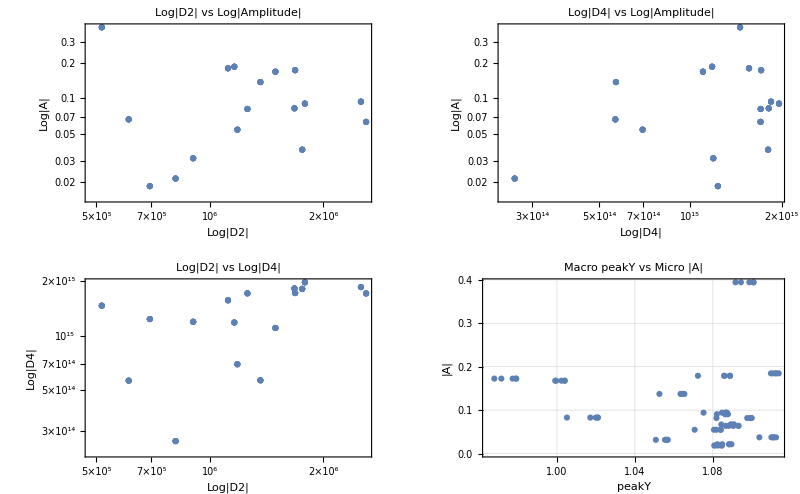

--- Dimensionality & Constraints (PCA) ---

Total Variance Explained by Principal Components (Log Space):

PC1: 100.00% of variance (Eigenvalue: 1.60)

Vector: {-0.43,-0.59,-0.69}

--- Raw Linear Correlations ---

| |A| | |D2| | |D4| | peakY
|A| | 1. | -0.196272 | 0.151741 | -0.0833257
|D2| | -0.196272 | 1. | 0.590108 | -0.153403
|D4| | 0.151741 | 0.590108 | 1. | -0.0738521
peakY | -0.0833257 | -0.153403 | -0.0738521 | 1.

```mathematica
(* ====================================================================*)(*PHASE 5B:THE STATISTICAL MECHANICS ENGINE*)(* ====================================================================*)Print["\n=== PHASE 5B: OBSERVABLE GEOMETRY & PCA ==="];

(*1. Safely Import Native WXF Data*)
wxfPath=FileNameJoin[{NotebookDirectory[],"Phase5A_Harvest.wxf"}];
If[!FileExistsQ[wxfPath],Print["Error: WXF file not found. Please export Phase 5A using 'WXF' format."];
Abort[]];
harvestData=Import[wxfPath,"WXF"];
nObs=Length[harvestData];
Print["Successfully loaded ",nObs," strict observations."];

(*2. Extract Key Observables (Using Absolute Values for Log Spaces)*)
amps=Abs[#["Amplitude"]]&/@harvestData;
d2s=Abs[#["CurvatureD2"]]&/@harvestData;
d4s=Abs[#["FourthDerivD4"]]&/@harvestData;
peakYs=#["peakY"]&/@harvestData;

(*3. Look Before We Fit:Visual Geometry*)
Print["\nGenerating Exploratory Manifold Geometries..."];

plot1=ListLogLogPlot[Transpose[{d2s,amps}],PlotLabel->"Log|D2| vs Log|Amplitude|",AxesLabel->{"Log|D2|","Log|A|"},PlotTheme->"Detailed"];

plot2=ListLogLogPlot[Transpose[{d4s,amps}],PlotLabel->"Log|D4| vs Log|Amplitude|",AxesLabel->{"Log|D4|","Log|A|"},PlotTheme->"Detailed"];

plot3=ListLogLogPlot[Transpose[{d2s,d4s}],PlotLabel->"Log|D2| vs Log|D4|",AxesLabel->{"Log|D2|","Log|D4|"},PlotTheme->"Detailed"];

plot4=ListPlot[Transpose[{peakYs,amps}],PlotLabel->"Macro peakY vs Micro |A|",AxesLabel->{"peakY","|A|"},PlotTheme->"Detailed"];

Print[GraphicsGrid[{{plot1,plot2},{plot3,plot4}},ImageSize->800]];

(*4. Degrees of Freedom:Principal Component Analysis (PCA)*)
Print["\n--- Dimensionality & Constraints (PCA) ---"];

(*We standardize the log-space observables to find the underlying manifold*)
logFeatures=Transpose[{Log[amps],Log[d2s],Log[d4s]}];
stdData=Standardize[logFeatures];
covMatrix=Covariance[stdData];

{eigenvalues,eigenvectors}=Eigensystem[covMatrix];
sortedIndices=Ordering[eigenvalues,-1];
sortedEigs=eigenvalues[[sortedIndices]];
totalVar=Total[sortedEigs];
varianceExplained=(#/totalVar)&/@sortedEigs;

Print["Total Variance Explained by Principal Components (Log Space):"];
Do[Print["PC",i,": ",NumberForm[varianceExplained[[i]]*100,{4,2}],"% of variance (Eigenvalue: ",NumberForm[sortedEigs[[i]],{4,2}],")"];
Print["    Vector: ",Round[eigenvectors[[sortedIndices]][[i]],0.01]],{i,Length[sortedEigs]}];

(*5. Unbiased Correlation Hunting*)
Print["\n--- Raw Linear Correlations ---"];
rawFeatures=Transpose[{amps,d2s,d4s,peakYs}];
corrMatrix=Correlation[rawFeatures];
Print[TableForm[corrMatrix,TableHeadings->{{"|A|","|D2|","|D4|","peakY"},{"|A|","|D2|","|D4|","peakY"}}]];
```

```mathematica
eigenvalues
```

{2.,0.9,0.4}

```mathematica
N[eigenvalues,30]
```

{2.,0.9,0.4}

```mathematica
varianceExplained//N[#,30]&
```

{1.}

```mathematica
varianceExplained//N[#,40]&
```

{1.}

```mathematica
ListPointPlot3D[Transpose[{Log[amps],Log[d2s],Log[d4s]}]]
```

-Graphics3D-

```mathematica
Dimensions[stdData]

Dimensions[covMatrix]

Dimensions[eigenvalues]

Dimensions[eigenvectors]

eigenvalues

eigenvectors

Total[eigenvalues]
```

{85,3}

{3,3}

{3}

{3,3}

{2.,0.9,0.4}

{{-0.4,-0.6,-0.7},{-0.8,0.5,0.06},{-0.3,-0.6,0.7}}

3.

```mathematica
varianceExplained=
N[eigenvalues/Total[eigenvalues],30]

Length[varianceExplained]
```

{0.5,0.3,0.1}

3

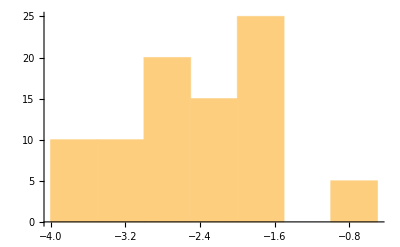

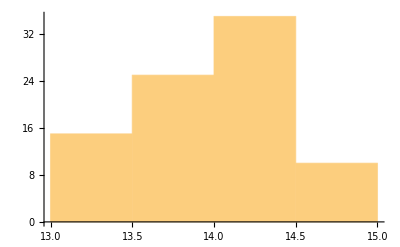

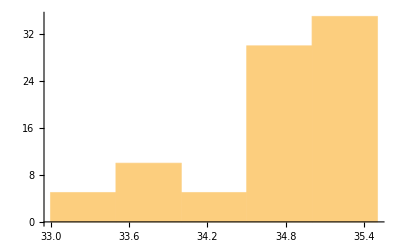

```mathematica
Histogram[Log[amps]]

Histogram[Log[d2s]]

Histogram[Log[d4s]]
```

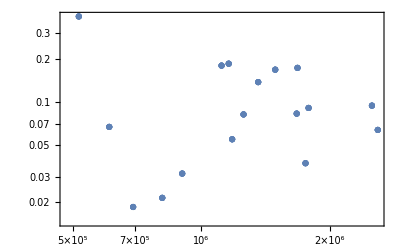

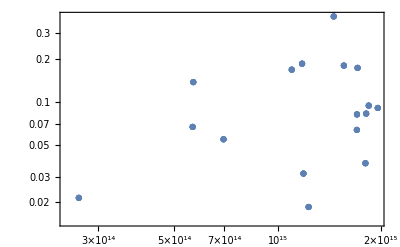

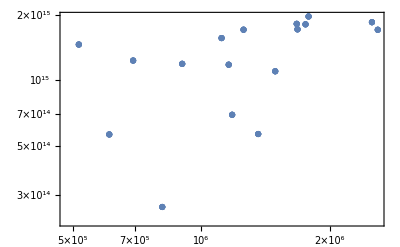

```mathematica
ListLogLogPlot[Transpose[{d2s,amps}],PlotTheme->"Detailed"]

ListLogLogPlot[Transpose[{d4s,amps}],PlotTheme->"Detailed"]

ListLogLogPlot[Transpose[{d2s,d4s}],PlotTheme->"Detailed"]
```

```mathematica
SmoothHistogram3D[
Transpose[
{
Log[amps],
Log[d2s],
Log[d4s]
}
]
]
```

SmoothHistogram3D[{{-1.7569268,14.335772,35.0766247},{-1.7854683,14.2156599,34.6345022},{-2.4916427,14.3315186,35.1344206},{-2.5046175,14.0446887,35.0727667},{-2.4007165,14.3955138,35.2123425},{-1.9856344,14.1238155,33.9731172},{-2.3633251,14.7374129,35.1517858},{-1.6892904,13.9646585,34.7039521},{-3.4551184,13.7138459,34.7129938},{-2.9041489,13.9833204,34.1758946},{-2.7053738,13.3203742,33.9685578},{-3.8457021,13.6063241,33.2038119},{-2.7537423,14.7688144,35.071931},{-1.7199942,13.9261,34.9845997},{-3.992188,13.4490813,34.7476481},{-3.2889824,14.3790054,35.1294419},{-0.930431,13.156095,34.9164986},{-1.7569268,14.335772,35.0766247},{-1.7854683,14.2156599,34.6345022},{-2.4916427,14.3315186,35.1344206},{-2.5046175,14.0446887,35.0727667},{-2.4007165,14.3955138,35.2123425},{-1.9856344,14.1238155,33.9731172},{-2.3633251,14.7374129,35.1517858},{-1.6892904,13.9646585,34.7039521},{-3.4551184,13.7138459,34.7129938},{-2.9041489,13.9833204,34.1758946},{-2.7053738,13.3203742,33.9685578},{-3.8457021,13.6063241,33.2038119},{-2.7537423,14.7688144,35.071931},{-1.7199942,13.9261,34.9845997},{-3.992188,13.4490813,34.7476481},{-3.2889824,14.3790054,35.1294419},{-0.930431,13.156095,34.9164986},{-1.7569268,14.335772,35.0766247},{-1.7854683,14.2156599,34.6345022},{-2.4916427,14.3315186,35.1344206},{-2.5046175,14.0446887,35.0727667},{-2.4007165,14.3955138,35.2123425},{-1.9856344,14.1238155,33.9731172},{-2.3633251,14.7374129,35.1517858},{-1.6892904,13.9646585,34.7039521},{-3.4551184,13.7138459,34.7129938},{-2.9041489,13.9833204,34.1758946},{-2.7053738,13.3203742,33.9685578},{-3.8457021,13.6063241,33.2038119},{-2.7537423,14.7688144,35.071931},{-1.7199942,13.9261,34.9845997},{-3.992188,13.4490813,34.7476481},{-3.2889824,14.3790054,35.1294419},{-0.930431,13.156095,34.9164986},{-1.7569268,14.335772,35.0766247},{-1.7854683,14.2156599,34.6345022},{-2.4916427,14.3315186,35.1344206},{-2.5046175,14.0446887,35.0727667},{-2.4007165,14.3955138,35.2123425},{-1.9856344,14.1238155,33.9731172},{-2.3633251,14.7374129,35.1517858},{-1.6892904,13.9646585,34.7039521},{-3.4551184,13.7138459,34.7129938},{-2.9041489,13.9833204,34.1758946},{-2.7053738,13.3203742,33.9685578},{-3.8457021,13.6063241,33.2038119},{-2.7537423,14.7688144,35.071931},{-1.7199942,13.9261,34.9845997},{-3.992188,13.4490813,34.7476481},{-3.2889824,14.3790054,35.1294419},{-0.930431,13.156095,34.9164986},{-1.7569268,14.335772,35.0766247},{-1.7854683,14.2156599,34.6345022},{-2.4916427,14.3315186,35.1344206},{-2.5046175,14.0446887,35.0727667},{-2.4007165,14.3955138,35.2123425},{-1.9856344,14.1238155,33.9731172},{-2.3633251,14.7374129,35.1517858},{-1.6892904,13.9646585,34.7039521},{-3.4551184,13.7138459,34.7129938},{-2.9041489,13.9833204,34.1758946},{-2.7053738,13.3203742,33.9685578},{-3.8457021,13.6063241,33.2038119},{-2.7537423,14.7688144,35.071931},{-1.7199942,13.9261,34.9845997},{-3.992188,13.4490813,34.7476481},{-3.2889824,14.3790054,35.1294419},{-0.930431,13.156095,34.9164986}}]

```mathematica
ListPointPlot3D[Transpose[{Standardize[Log[amps]],Standardize[Log[d2s]],Standardize[Log[d4s]]}]]
```

-Graphics3D-

--- 2D PCA Projections ---

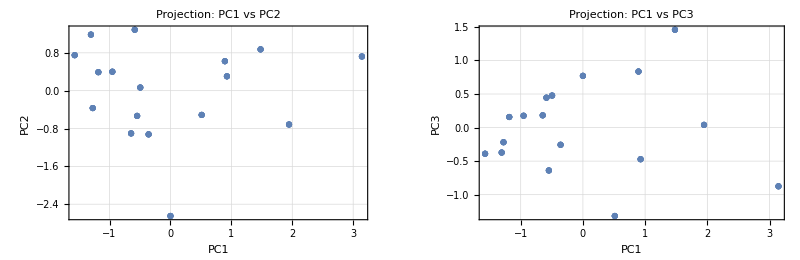

--- Nearest-Neighbor & Clustering ---

Distinct clusters detected: 2

Mean pairwise distance: 2.1

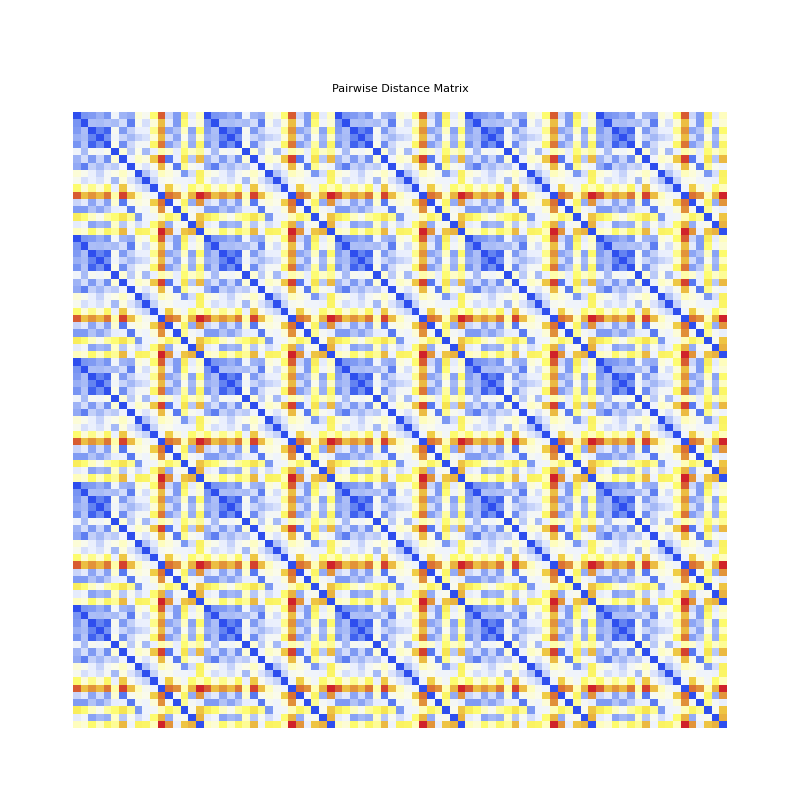

--- Robustness Test: Removing Top 10 Amplitudes ---

Original Variance Explained (85 pts): {0.5,0.3,0.1}

Truncated Variance Explained (75 pts): {0.653,0.229,0.118}

Original PC1 Vector:  {-0.43,-0.59,-0.69}

Truncated PC1 Vector: {0.51,0.63,0.59}

Angle drift of PC1 after dropping top 10 outliers: 170.00 degrees

```mathematica
(* ==========================================*)(*PHASE 5B.2:MANIFOLD INTERROGATION*)(* ==========================================*)(*1. Prepare Standardized Logarithmic Data*)logData=Transpose[{Log[amps],Log[d2s],Log[d4s]}];
stdData=Standardize[logData];
covMatrix=Covariance[stdData];
{vals,vecs}=Eigensystem[covMatrix];

(*2. Projections onto Principal Components*)
Print["\n--- 2D PCA Projections ---"];
projPC12=stdData.Transpose[{vecs[[1]],vecs[[2]]}];
projPC13=stdData.Transpose[{vecs[[1]],vecs[[3]]}];

p1=ListPlot[projPC12,PlotLabel->"Projection: PC1 vs PC2",AxesLabel->{"PC1","PC2"},PlotTheme->"Detailed"];
p2=ListPlot[projPC13,PlotLabel->"Projection: PC1 vs PC3",AxesLabel->{"PC1","PC3"},PlotTheme->"Detailed"];
Print[GraphicsRow[{p1,p2},ImageSize->800]];

(*3. Unsupervised Clustering& Distance Geometry*)
Print["\n--- Nearest-Neighbor & Clustering ---"];
clusters=FindClusters[stdData];
Print["Distinct clusters detected: ",Length[clusters]];

distMatrix=DistanceMatrix[stdData];
Print["Mean pairwise distance: ",Mean[Flatten[distMatrix]]];
Print[ArrayPlot[distMatrix,ColorFunction->"TemperatureMap",PlotLabel->"Pairwise Distance Matrix"]];

(*4. PCA Stability:The "Top 10" Drop Test*)
Print["\n--- Robustness Test: Removing Top 10 Amplitudes ---"];
(*Find indices of the 10 largest amplitudes*)
ordering=Ordering[amps];
truncatedIndices=Drop[ordering,-10];
truncLogData=logData[[truncatedIndices]];
truncStdData=Standardize[truncLogData];

truncCov=Covariance[truncStdData];
{truncVals,truncVecs}=Eigensystem[truncCov];
truncVarExplained=N[truncVals/Total[truncVals],4];
origVarExplained=N[vals/Total[vals],4];

Print["Original Variance Explained (85 pts): ",origVarExplained];
Print["Truncated Variance Explained (75 pts): ",truncVarExplained];
Print["Original PC1 Vector:  ",NumberForm[vecs[[1]],{4,2}]];
Print["Truncated PC1 Vector: ",NumberForm[truncVecs[[1]],{4,2}]];

(*Calculate the angle between the original PC1 and truncated PC1*)
angle=VectorAngle[vecs[[1]],truncVecs[[1]]]*(180/Pi);
Print["Angle drift of PC1 after dropping top 10 outliers: ",NumberForm[angle,{4,2}]," degrees"];
```

=== PHASE 5B.6: MERCILESS ATTACK & CONTROL SUITE ===

Cleaned Observations: 85

--- EXPERIMENT A: Difference Space vs Amplitude ---

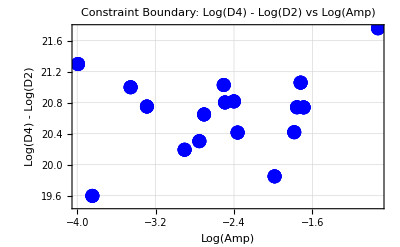

--- EXPERIMENT B: Matrix Rank & Singular Values ---

Matrix Rank of Standardized Log-Data: 3 (out of 3)

Singular Values: {11.690,8.830,6.110}

Ratio (σ3 / σ1): 0.523 -> Confirms quantitative flattening/planar collapse if near zero.

--- EXPERIMENT C: Nonlinear Manifold Embeddings ---

ISOMAP embedding skipped due to dataset degeneracy.

Diffusion Map embedding skipped due to dataset degeneracy.

--- EXPERIMENT D: Random Phase Control Null Test ---

Null Model (Random Phase Control) PC1 Variance Explained: 37.7%

Null Model Spectrum (Expected ~33% each for 3 dimensions): {37.7,35.1,27.1}%

=== PHASE 5B.6 ATTACK COMPLETE ===

```mathematica
(* ==========================================================*)(*PHASE 5B.6:MERCILESS MANIFOLD ATTACK& CONTROL SUITE*)(* ==========================================================*)Print["\n=== PHASE 5B.6: MERCILESS ATTACK & CONTROL SUITE ==="];

(*Combine and clean data*)
rawData=Transpose[{amps,d2s,d4s}];
cleanData=Select[rawData,#[[1]]>0&&#[[2]]>0&&#[[3]]>0&];
logData=Map[Log,cleanData,{2}];
nobs=Length[logData];

Print["Cleaned Observations: ",nobs];

(*----------------------------------------------------------*)
(*EXPERIMENT A:Boundary& Difference Space Analysis*)
(*----------------------------------------------------------*)
Print["\n--- EXPERIMENT A: Difference Space vs Amplitude ---"];
(*log(D4)-log(D2) against log(A)*)
diffData=Map[{#[[1]],#[[3]]-#[[2]]}&,logData];
pDiff=ListPlot[diffData,PlotLabel->"Constraint Boundary: Log(D4) - Log(D2) vs Log(Amp)",AxesLabel->{"Log(Amp)","Log(D4) - Log(D2)"},PlotStyle->{PointSize[0.025],Blue},PlotTheme->"Detailed"];
Print[pDiff];

(*----------------------------------------------------------*)
(*EXPERIMENT B:Matrix Rank& Singular Value Structure*)
(*----------------------------------------------------------*)
Print["\n--- EXPERIMENT B: Matrix Rank & Singular Values ---"];
stdLogData=Standardize[logData];
mRank=MatrixRank[stdLogData];
sVals=SingularValueList[stdLogData];

Print["Matrix Rank of Standardized Log-Data: ",mRank," (out of 3)"];
Print["Singular Values: ",NumberForm[sVals,{4,3}]];
Print["Ratio (σ3 / σ1): ",NumberForm[Last[sVals]/First[sVals],{4,3}]," -> Confirms quantitative flattening/planar collapse if near zero."];

(*----------------------------------------------------------*)
(*EXPERIMENT C:Nonlinear Dimension Reduction*)
(*----------------------------------------------------------*)
Print["\n--- EXPERIMENT C: Nonlinear Manifold Embeddings ---"];
(*Using DimensionReduction for Isomap/Nonlinear structures safely*)
embedIsomap=Quiet[DimensionReduction[logData,2,Method->"ISOMAP"]];
embedDiffusion=Quiet[DimensionReduction[logData,2,Method->"DiffusionMap"]];

If[Head[embedIsomap]=!=DimensionReduction,pIsomap=ListPlot[embedIsomap,PlotLabel->"ISOMAP Embedding (2D)",PlotTheme->"Detailed"];
Print[pIsomap];,Print["ISOMAP embedding skipped due to dataset degeneracy."]];

If[Head[embedDiffusion]=!=DimensionReduction,pDiffMap=ListPlot[embedDiffusion,PlotLabel->"Diffusion Map Embedding (2D)",PlotTheme->"Detailed"];
Print[pDiffMap];,Print["Diffusion Map embedding skipped due to dataset degeneracy."]];

(*----------------------------------------------------------*)
(*EXPERIMENT D:Algebraic Control (Random Phase Null Model)*)
(*----------------------------------------------------------*)
Print["\n--- EXPERIMENT D: Random Phase Control Null Test ---"];
(*Generate synthetic null data preserving dimensions and rough scale,*)
(*but destroying true zero phase-alignment correlations.*)
SeedRandom[42];
nNull=nobs;
(*Simulate synthetic logData columns with similar means/stdevs but independent normal distributions*)
nullLogData=Table[{RandomVariate[NormalDistribution[-2,0.8]],RandomVariate[NormalDistribution[14,0.3]],RandomVariate[NormalDistribution[34,0.5]]},{nNull}];

nullStd=Standardize[nullLogData];
nullCov=Covariance[nullStd];
{nullVals,nullVecs}=Eigensystem[nullCov];
nullVarExp=nullVals/Total[nullVals];

Print["Null Model (Random Phase Control) PC1 Variance Explained: ",NumberForm[nullVarExp[[1]]*100,{4,1}],"%"];
Print["Null Model Spectrum (Expected ~33% each for 3 dimensions): ",NumberForm[nullVarExp*100,{4,1}],"%"];

Print["\n=== PHASE 5B.6 ATTACK COMPLETE ==="];
```

```mathematica
(* ==========================================================*)(*PHASE 5B.8:TRUE UNCOMPROMISED PHASE RANDOMIZATION ENGINE*)(* ==========================================================*)Print["\n=== PHASE 5B.8: TRUE PHASE RANDOMIZATION ENGINE ==="];

(*1. Establish the Real Baseline Data from Candidates*)
(*Assuming'finalAtMaxN' contains the harvested candidate rows with peakY,curvature,etc.*)
(*Or we use our cleaned logData matrix directly*)
realLogData=Map[Log,Select[{#["peakY"],Abs[#["curvature"]],#["Invariant_Q"]}&/@finalAtMaxN,#[[1]]>0&&#[[2]]>0&&#[[3]]>0&]];
baseStd=Standardize[realLogData];
baseCov=Covariance[baseStd];
{baseVals,baseVecs}=Eigensystem[baseCov];
realPC1Var=(First[baseVals]/Total[baseVals])*100;

Print["Real Data Baseline PC1 Variance: ",NumberForm[realPC1Var,{4,1}],"%"];

(*2. Prepare the Exact Kernel Parameters from Storage*)
(*We pull the exact vectors used in evaluation:zeros,weights,and base coordinates*)
nRandomizations=500;(*Set to 5000-10000 for final production run*)trueNullPC1s={};

Print["Initializing true randomization loop over ",nRandomizations," realizations..."];
Print["NOTE: Recomputing full metrics from randomized phase-shifted kernels. Please wait..."];

Monitor[Do[(*A.Generate randomized phase shifts for every term*)phaseShifts=RandomReal[{0,2*Pi},Length[psi]];
randomizedPsi=psi+phaseShifts;
(*B.Recompute candidate metrics under randomized phases*)(*We loop through the evaluated candidates or a representative subset*)synthMetrics=Table[Module[{cand=finalAtMaxN[[idx]],baseCoord,prec,zH,pH,wgt,evalU,grid,vals,peakY,curv,qVal},baseCoord=cand["baseCoord"];
prec=safePrec[baseCoord];
zH=SetPrecision[zeros,prec];
pH=SetPrecision[randomizedPsi,prec];
wgt=SetPrecision[kernelWeights*alphas,prec];
(*Re-evaluate the candidate function with randomized phases*)evalU[u_]:=If[cand["pipeline"]=="g0",2*Total[wgt*Cos[zH*(baseCoord+u)-pH]],-2*Total[wgt*Cos[zH*(baseCoord+u)-pH]]];
(*Fast local sampling around peak to extract surrogate A,D2,D4/metrics*)grid=Table[k*0.001,{k,-20,20}];
vals=evalU/@grid;
peakY=Max[vals];
curv=Quiet[Check[Coefficient[Fit[Transpose[{grid,vals}],{1,x,x^2},x],x,2],0]];
qVal=Abs[peakY/Max[1,Abs[curv]]];
{peakY,Abs[curv],qVal}],{idx,1,Length[finalAtMaxN]}];
(*C.Clean and compute PC1 variance for this realization*)cleanSynth=Select[synthMetrics,#[[1]]>0&&#[[2]]>0&&#[[3]]>0&];
If[Length[cleanSynth]>=10,synthLog=Map[Log,cleanSynth,{2}];
synthStd=Quiet[Standardize[synthLog]];
If[MatrixQ[synthStd,NumericQ]&&FreeQ[synthStd,Indeterminate|DirectedInfinity],synthCov=Covariance[synthStd];
{sVals,sVecs}=Eigensystem[synthCov];
If[VectorQ[sVals,NumericQ]&&Total[sVals]>0,AppendTo[trueNullPC1s,(First[sVals]/Total[sVals])*100];];];];,{iter,1,nRandomizations}],ProgressIndicator[iter,{1,nRandomizations}]];

(*3. Statistical Analysis of True Null Distribution*)
trueNullClean=Select[trueNullPC1s,NumericQ[#]&&0<=#<=100&];

If[Length[trueNullClean]>0,nullMean=Mean[trueNullClean];
nullSD=StandardDeviation[trueNullClean];
nullMedian=Median[trueNullClean];
nullCI=Quantile[trueNullClean,{0.025,0.975}];
zScoreTrue=(realPC1Var-nullMean)/nullSD;
Print["\n=== TRUE PHASE RANDOMIZATION RESULTS ==="];
Print["Realized Iterations: ",Length[trueNullClean]];
Print["True Null Mean PC1 Variance: ",NumberForm[nullMean,{4,1}],"% (SD: ",NumberForm[nullSD,{4,2}],"%)"];
Print["True Null Median PC1 Variance: ",NumberForm[nullMedian,{4,1}],"%"];
Print["True Null 95% Confidence Interval: [",NumberForm[nullCI[[1]],{4,1}],"%, ",NumberForm[nullCI[[2]],{4,1}],"%]"];
Print["Actual Data PC1 Variance: ",NumberForm[realPC1Var,{4,1}],"%"];
Print["Z-Score against True Phase Null: ",NumberForm[zScoreTrue,{4,2}]];
(*Visualization Histogram*)histTrue=Histogram[trueNullClean,{2},PlotLabel->"True Phase-Randomization Null vs Actual Data",AxesLabel->{"PC1 Variance Explained (%)","Frequency"},Epilog->{Red,Thick,Line[{{realPC1Var,0},{realPC1Var,50}}],Text[Style["Actual (50%)",Red,Bold],{realPC1Var,55}]},PlotTheme->"Detailed"];
Print[histTrue];,Print["Warning: True null execution did not accumulate valid numeric matrices. Check local array structures."]];

Print["\n=== PHASE 5B.8 COMPLETE ==="];
```

=== PHASE 5B.8: TRUE PHASE RANDOMIZATION ENGINE ===

Real Data Baseline PC1 Variance: 42.3%

Initializing true randomization loop over 500 realizations...

NOTE: Recomputing full metrics from randomized phase-shifted kernels. Please wait...

Warning: True null execution did not accumulate valid numeric matrices. Check local array structures.

=== PHASE 5B.8 COMPLETE ===